```mathematica
ClearAll["Global`*"]
```

### Solve the first order perturbation case using Fourier transform (aka solving it with a hammer) .

```mathematica
FourierTransform[Sin[f(Pi x)/(2L)],x,k]
```

ⅈ √(2 π) DiracDelta[2 k-(f π)/L]-ⅈ √(2 π) DiracDelta[2 k+(f π)/L]

Perturbative approach: V = V0 + η V1
ρ = ρ0 + η ρ1

```mathematica
Va[x_] = 0 + η signA V1a Sin[f(Pi x)/(2 L)];
Vb[x_] = 0 + η signB V1b Sin[f(Pi x)/(2 L)];
Vc[x_] = 0 + η signC V1c Sin[f(Pi x)/(2 L)];
```

Solving: D ∂ρ_0+η (D∂(ρ_1+∂W ρ_0))= K_0 ρ_0+η ((K_0 W + Ξ Exp[V])+K_0 ρ_1)

#### Find the η^0 solutions:

D ∂ρ_0= K_0 ρ_0

```mathematica
rhosol = Solve[{-(Exp[-Eab]+Exp[-Eac] Aac)ρA0 + Exp[-Eab] ρB0 + Exp[-Eac] ρC0 == 0, -(Exp[-Eab]+Exp[-Ebc])ρB0 + Exp[-Eab] ρA0 + Exp[-Ebc] ρC0 ==0},{ρA0,ρB0, ρC0}]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ρB0→((Aac ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) ρA0)/(ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc),ρC0→((ⅇ^Eac+Aac (ⅇ^Eab+ⅇ^Ebc)) ρA0)/(ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc)}}

```mathematica
{rhoB0, rhoC0} = {rhosol[[1,1,2]], rhosol[[1,2,2]]}
```

{((Aac ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) ρA0)/(ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc),((ⅇ^Eac+Aac (ⅇ^Eab+ⅇ^Ebc)) ρA0)/(ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc)}

```mathematica
rhoA0 = Solve[2(ρA0 + rhoB0 + rhoC0) == ρ, ρA0][[1,1,2]]//Simplify
```

((ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) ρ)/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc))

```mathematica
{rhoB0, rhoC0} = {rhoB0, rhoC0} /. ρA0 -> rhoA0 //Simplify
```

{((Aac ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) ρ)/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc)),((ⅇ^Eac+Aac (ⅇ^Eab+ⅇ^Ebc)) ρ)/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc))}

#### Out - of - equilibrium solution :

Solve η (D∂(ρ_1+∂W ρ_0))= η ((K_0 W + Ξ Exp[V])+K_0 ρ_1) using the ρ_0 found above.

```mathematica
K0 = {{-Exp[-Eab]-Exp[-Eac] Aac,Exp[-Eab],Exp[-Eac]},{Exp[-Eab],-Exp[-Eab]-Exp[-Ebc],Exp[-Ebc]},{Exp[-Eac] Aac,Exp[-Ebc],-Exp[-Ebc]-Exp[-Eac]}}
```

{{-ⅇ^-Eab-Aac ⅇ^-Eac,ⅇ^-Eab,ⅇ^-Eac},{ⅇ^-Eab,-ⅇ^-Eab-ⅇ^-Ebc,ⅇ^-Ebc},{Aac ⅇ^-Eac,ⅇ^-Ebc,-ⅇ^-Eac-ⅇ^-Ebc}}

```mathematica
Ksi = {{Exp[-Eab] (V1a+V1b)+Exp[-Eac] (V1a+V1c) Aac,-Exp[-Eab] (V1a+V1b),-Exp[-Eac] (V1a+V1c)},{-Exp[-Eab] (V1a+V1b),Exp[-Eab] (V1a+V1b)+Exp[-Ebc] (V1b+V1c),-Exp[-Ebc] (V1b+V1c)},{-Exp[-Eac] (V1a+V1c) Aac,-Exp[-Ebc] (V1b+V1c),Exp[-Ebc] (V1b+V1c)+Exp[-Eac] (V1a+V1c)}}Sin[f(Pi x)/(2 L)]
```

{{(ⅇ^-Eab (V1a+V1b)+Aac ⅇ^-Eac (V1a+V1c)) Sin[(f π x)/(2 L)],-ⅇ^-Eab (V1a+V1b) Sin[(f π x)/(2 L)],-ⅇ^-Eac (V1a+V1c) Sin[(f π x)/(2 L)]},{-ⅇ^-Eab (V1a+V1b) Sin[(f π x)/(2 L)],(ⅇ^-Eab (V1a+V1b)+ⅇ^-Ebc (V1b+V1c)) Sin[(f π x)/(2 L)],-ⅇ^-Ebc (V1b+V1c) Sin[(f π x)/(2 L)]},{-Aac ⅇ^-Eac (V1a+V1c) Sin[(f π x)/(2 L)],-ⅇ^-Ebc (V1b+V1c) Sin[(f π x)/(2 L)],(ⅇ^-Eac (V1a+V1c)+ⅇ^-Ebc (V1b+V1c)) Sin[(f π x)/(2 L)]}}

```mathematica
(*It's interesting to consider whether the sign should be here. However, it's just an assumption. Let's say, we take the absolute values. It's consistent in both codes.*)
```

```mathematica
W = {{signA V1a,0,0},{0,signB V1b,0},{0,0,signC V1c}}Sin[f(Pi x)/(2 L)]
```

{{signA V1a Sin[(f π x)/(2 L)],0,0},{0,signB V1b Sin[(f π x)/(2 L)],0},{0,0,signC V1c Sin[(f π x)/(2 L)]}}

```mathematica
Dm = {{1,0,0},{0,1,0},{0,0,1}} (*Hugo's units: x measured in x/√(D/Subscript[k^0, AB]). To convert, set diffusion constant to 1.*)
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
FMooe = (-f^2 π^2)/(4 L^2)Dm-K0
```

{{ⅇ^-Eab+Aac ⅇ^-Eac-(f^2 π^2)/(4 L^2),-ⅇ^-Eab,-ⅇ^-Eac},{-ⅇ^-Eab,ⅇ^-Eab+ⅇ^-Ebc-(f^2 π^2)/(4 L^2),-ⅇ^-Ebc},{-Aac ⅇ^-Eac,-ⅇ^-Ebc,ⅇ^-Eac+ⅇ^-Ebc-(f^2 π^2)/(4 L^2)}}

This matrix is singular for a particular choice of parameters :

```mathematica
AacSing = Solve[Det[FMooe]==0,Aac][[1,1,2]]
```

(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) f^2 L^2 π^2+4 ⅇ^(Eab+Ebc) f^2 L^2 π^2+8 ⅇ^(Eac+Ebc) f^2 L^2 π^2-ⅇ^(Eab+Eac+Ebc) f^4 π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) f^2 π^2))

```mathematica
AacSing/.{Eab -> 0.2,Ebc->0.5,Eac->0.5,L->1}
```

(-151.44+453.126 f^2-323.41 f^4)/(4 (16.3661-19.8749 f^2))

A reasonable way to circumvent this would be to use the pseudoinverse for these values . HOWEVER, it does not compile . Therefore, I just avoid this parameter regime in the future because my expansion breaks down around it .

```mathematica
(*FMooeSing = FMooe/.Aac->(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))//FullSimplify*)
```

```mathematica
(*PseudoInverse[FMooeSing]*)
```

So, solve the equation, having in mind that it only works when FMooe is not singular .

```mathematica
solooe = Solve[FMooe.{x,y,z} == {a1,b1,c1},{x,y,z}]
```

{{x→-((4 L^2 (16 a1 ⅇ^Eab L^4+16 b1 ⅇ^Eab L^4+16 c1 ⅇ^Eab L^4+16 a1 ⅇ^Eac L^4+16 b1 ⅇ^Eac L^4+16 c1 ⅇ^Eac L^4+16 a1 ⅇ^Ebc L^4+16 b1 ⅇ^Ebc L^4+16 c1 ⅇ^Ebc L^4-8 a1 ⅇ^(Eab+Eac) f^2 L^2 π^2-4 a1 ⅇ^(Eab+Ebc) f^2 L^2 π^2-4 c1 ⅇ^(Eab+Ebc) f^2 L^2 π^2-4 a1 ⅇ^(Eac+Ebc) f^2 L^2 π^2-4 b1 ⅇ^(Eac+Ebc) f^2 L^2 π^2+a1 ⅇ^(Eab+Eac+Ebc) f^4 π^4))/(f^2 π^2 (16 ⅇ^Eab L^4+32 Aac ⅇ^Eab L^4+48 ⅇ^Eac L^4+32 ⅇ^Ebc L^4+16 Aac ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2-4 ⅇ^(Eab+Ebc) f^2 L^2 π^2-4 Aac ⅇ^(Eab+Ebc) f^2 L^2 π^2-8 ⅇ^(Eac+Ebc) f^2 L^2 π^2+ⅇ^(Eab+Eac+Ebc) f^4 π^4))),y→-((4 L^2 (16 a1 Aac ⅇ^Eab L^4+16 Aac b1 ⅇ^Eab L^4+16 Aac c1 ⅇ^Eab L^4+16 a1 ⅇ^Eac L^4+16 b1 ⅇ^Eac L^4+16 c1 ⅇ^Eac L^4+16 a1 ⅇ^Ebc L^4+16 b1 ⅇ^Ebc L^4+16 c1 ⅇ^Ebc L^4-4 b1 ⅇ^(Eab+Eac) f^2 L^2 π^2-4 c1 ⅇ^(Eab+Eac) f^2 L^2 π^2-4 b1 ⅇ^(Eab+Ebc) f^2 L^2 π^2-4 Aac b1 ⅇ^(Eab+Ebc) f^2 L^2 π^2-4 a1 ⅇ^(Eac+Ebc) f^2 L^2 π^2-4 b1 ⅇ^(Eac+Ebc) f^2 L^2 π^2+b1 ⅇ^(Eab+Eac+Ebc) f^4 π^4))/(f^2 π^2 (16 ⅇ^Eab L^4+32 Aac ⅇ^Eab L^4+48 ⅇ^Eac L^4+32 ⅇ^Ebc L^4+16 Aac ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2-4 ⅇ^(Eab+Ebc) f^2 L^2 π^2-4 Aac ⅇ^(Eab+Ebc) f^2 L^2 π^2-8 ⅇ^(Eac+Ebc) f^2 L^2 π^2+ⅇ^(Eab+Eac+Ebc) f^4 π^4))),z→-((4 (16 a1 Aac ⅇ^Eab L^6+16 Aac b1 ⅇ^Eab L^6+16 Aac c1 ⅇ^Eab L^6+16 a1 ⅇ^Eac L^6+16 b1 ⅇ^Eac L^6+16 c1 ⅇ^Eac L^6+16 a1 Aac ⅇ^Ebc L^6+16 Aac b1 ⅇ^Ebc L^6+16 Aac c1 ⅇ^Ebc L^6-4 b1 ⅇ^(Eab+Eac) f^2 L^4 π^2-4 c1 ⅇ^(Eab+Eac) f^2 L^4 π^2-4 a1 Aac ⅇ^(Eab+Ebc) f^2 L^4 π^2-4 Aac c1 ⅇ^(Eab+Ebc) f^2 L^4 π^2-8 c1 ⅇ^(Eac+Ebc) f^2 L^4 π^2+c1 ⅇ^(Eab+Eac+Ebc) f^4 L^2 π^4))/(f^2 π^2 (16 ⅇ^Eab L^4+32 Aac ⅇ^Eab L^4+48 ⅇ^Eac L^4+32 ⅇ^Ebc L^4+16 Aac ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2-4 ⅇ^(Eab+Ebc) f^2 L^2 π^2-4 Aac ⅇ^(Eab+Ebc) f^2 L^2 π^2-8 ⅇ^(Eac+Ebc) f^2 L^2 π^2+ⅇ^(Eab+Eac+Ebc) f^4 π^4)))}}

```mathematica
RHS = (K0.W+ Ksi- Dm.D[W,{x,2}]).{ρA0,ρB0,ρC0}//FullSimplify
```

{(ⅇ^(-Eab-Eac) (-4 ⅇ^Eac L^2 (V1a ((-1+signA) ρA0+ρB0)-V1b (ρA0+(-1+signB) ρB0))+ⅇ^Eab (ⅇ^Eac f^2 π^2 signA V1a ρA0+4 L^2 (Aac (V1a-signA V1a+V1c) ρA0-(V1a+V1c-signC V1c) ρC0))) Sin[(f π x)/(2 L)])/(4 L^2),(ⅇ^(-Eab-Ebc) (4 ⅇ^Ebc L^2 (V1a ((-1+signA) ρA0+ρB0)-V1b (ρA0+(-1+signB) ρB0))+ⅇ^Eab (ⅇ^Ebc f^2 π^2 signB V1b ρB0+4 L^2 (-V1b ((-1+signB) ρB0+ρC0)+V1c (ρB0+(-1+signC) ρC0)))) Sin[(f π x)/(2 L)])/(4 L^2),(ⅇ^(-Eac-Ebc) (4 ⅇ^Ebc L^2 (Aac ((-1+signA) V1a-V1c) ρA0+(V1a+V1c-signC V1c) ρC0)+ⅇ^Eac (ⅇ^Ebc f^2 π^2 signC V1c ρC0+4 L^2 (V1b ((-1+signB) ρB0+ρC0)-V1c (ρB0+(-1+signC) ρC0)))) Sin[(f π x)/(2 L)])/(4 L^2)}

```mathematica
a1 = RHS[[1]]//Simplify;
b1 = RHS[[2]]//Simplify;
c1 = RHS[[3]]//Simplify;
```

Compare solutions at equilibrium :

```mathematica
solooe//FullSimplify
```

{{x→-(((-8 ⅇ^(Eab+Eac) f^2 L^2 π^2 signA V1a ρA0+ⅇ^(Eab+Eac+Ebc) f^4 π^4 signA V1a ρA0+4 Aac L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) f^2 π^2) ((-1+signA) V1a-V1c) ρA0-4 ⅇ^(Eac+Ebc) f^2 L^2 π^2 (-((V1a-2 signA V1a+V1b) ρA0)+(V1a+V1b) ρB0)-4 ⅇ^(Eab+Ebc) f^2 L^2 π^2 (signA V1a ρA0+(V1a+V1c) ρC0)+16 ⅇ^Eab L^4 (signA V1a ρA0+(V1b+V1c) ρB0+(2 V1a-V1b+V1c) ρC0)+16 ⅇ^Eac L^4 ((-2+3 signA) V1a ρA0+2 V1a ρB0+V1c (-ρB0+ρC0)+V1b (-2 ρA0+ρB0+ρC0))+16 ⅇ^Ebc L^4 (V1b (-ρA0+ρB0)+V1c ρC0+V1a ((-1+2 signA) ρA0+ρB0+ρC0))) Sin[(f π x)/(2 L)])/(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) f^2 L^2 π^2+ⅇ^(Eab+Eac) f^4 π^4))),y→-(((-4 ⅇ^(Eab+Ebc) f^2 L^2 π^2 signB V1b ρB0+ⅇ^(Eab+Eac+Ebc) f^4 π^4 signB V1b ρB0-4 ⅇ^(Eac+Ebc) f^2 L^2 π^2 ((V1a+V1b) ρA0-(V1a+V1b-2 signB V1b) ρB0)-4 ⅇ^(Eab+Eac) f^2 L^2 π^2 (-((V1b-2 signB V1b+V1c) ρB0)+(V1b+V1c) ρC0)+16 ⅇ^Ebc L^4 (V1b (ρA0-ρB0+2 signB ρB0)+V1c ρC0+V1a (ρA0-ρB0+ρC0))+16 ⅇ^Eab L^4 (-V1c ρB0-V1a ρC0+V1b ((-1+signB) ρB0+ρC0))+16 ⅇ^Eac L^4 (V1a (ρA0-ρB0)+V1c (-ρB0+ρC0)+V1b (ρA0-2 ρB0+3 signB ρB0+ρC0))+4 Aac L^2 (-ⅇ^(Eab+Ebc) f^2 π^2 signB V1b ρB0+4 ⅇ^Ebc L^2 (-V1c ρA0-V1a ρB0+V1b (ρA0+(-1+signB) ρB0))+4 ⅇ^Eab L^2 (V1a ρA0+V1c (ρA0-ρB0+ρC0)+V1b (-ρB0+2 signB ρB0+ρC0)))) Sin[(f π x)/(2 L)])/(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) f^2 L^2 π^2+ⅇ^(Eab+Eac) f^4 π^4))),z→-(((-8 ⅇ^(Eac+Ebc) f^2 L^2 π^2 signC V1c ρC0+ⅇ^(Eab+Eac+Ebc) f^4 π^4 signC V1c ρC0-16 ⅇ^Eab L^4 (V1a+V1c-signC V1c) ρC0-32 ⅇ^Ebc L^4 (V1a+V1c-signC V1c) ρC0+4 ⅇ^(Eab+Ebc) f^2 L^2 π^2 (V1a+V1c-signC V1c) ρC0-4 ⅇ^(Eab+Eac) f^2 L^2 π^2 ((V1b+V1c) ρB0-(V1b+V1c-2 signC V1c) ρC0)+16 ⅇ^Eac L^4 (V1a (ρA0-ρB0)+V1b (ρA0+ρB0-2 ρC0)+V1c (2 ρB0-2 ρC0+3 signC ρC0))+4 Aac L^2 (-ⅇ^(Eab+Ebc) f^2 π^2 ((V1a+V1c) ρA0+signC V1c ρC0)+4 ⅇ^Ebc L^2 (-V1b ρA0+2 V1c ρA0+V1b ρB0+V1a (ρA0+ρB0)+signC V1c ρC0)+4 ⅇ^Eab L^2 (V1a ρA0+V1b (ρB0-ρC0)+V1c (ρA0+ρB0-ρC0+2 signC ρC0)))) Sin[(f π x)/(2 L)])/(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) f^2 L^2 π^2+ⅇ^(Eab+Eac) f^4 π^4)))}}

```mathematica
{ρA0, ρB0, ρC0} = {rhoA0, rhoB0, rhoC0}
```

{((ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) ρ)/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc)),((Aac ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) ρ)/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc)),((ⅇ^Eac+Aac (ⅇ^Eab+ⅇ^Ebc)) ρ)/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc))}

The solutions are:

```mathematica
RhoA[x_] = ρA0 + η solooe[[1,1,2]]//FullSimplify
RhoB[x_] =ρB0 + η solooe[[1,2,2]]//FullSimplify
RhoC[x_] =ρC0 +η solooe[[1,3,2]]//FullSimplify
```

1/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc))ρ (ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc-((16 (1+2 Aac) ⅇ^(2 Eab) L^4 signA V1a+48 ⅇ^(2 Eac) L^4 signA V1a+16 (2+Aac) ⅇ^(2 Ebc) L^4 signA V1a-8 ⅇ^(2 Eab+Eac) f^2 L^2 π^2 signA V1a-8 ⅇ^(Eab+2 Eac) f^2 L^2 π^2 signA V1a-4 (1+Aac) ⅇ^(2 Eab+Ebc) f^2 L^2 π^2 signA V1a-8 ⅇ^(2 Eac+Ebc) f^2 L^2 π^2 signA V1a-4 (1+Aac) ⅇ^(Eab+2 Ebc) f^2 L^2 π^2 signA V1a-8 ⅇ^(Eac+2 Ebc) f^2 L^2 π^2 signA V1a+ⅇ^(2 Eab+Eac+Ebc) f^4 π^4 signA V1a+ⅇ^(Eab+2 Eac+Ebc) f^4 π^4 signA V1a+ⅇ^(Eab+Eac+2 Ebc) f^4 π^4 signA V1a+16 ⅇ^(Eac+Ebc) L^4 (V1a-Aac V1a+(5+Aac) signA V1a+(-1+Aac) V1b)+32 ⅇ^(Eab+Eac) L^4 ((2+Aac) signA V1a+(-1+Aac) (V1b-V1c))-4 ⅇ^(Eab+Eac+Ebc) f^2 L^2 π^2 ((5+Aac) signA V1a+(-1+Aac) (V1b-V1c))+16 ⅇ^(Eab+Ebc) L^4 ((-1+Aac+3 (1+Aac) signA) V1a+V1c-Aac V1c)) η Sin[(f π x)/(2 L)])/(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) f^2 L^2 π^2+ⅇ^(Eab+Eac) f^4 π^4)))

1/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc))ρ (Aac ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc-((16 Aac (1+2 Aac) ⅇ^(2 Eab) L^4 signB V1b+48 ⅇ^(2 Eac) L^4 signB V1b+16 (2+Aac) ⅇ^(2 Ebc) L^4 signB V1b-8 Aac ⅇ^(2 Eab+Eac) f^2 L^2 π^2 signB V1b-8 ⅇ^(Eab+2 Eac) f^2 L^2 π^2 signB V1b-4 Aac (1+Aac) ⅇ^(2 Eab+Ebc) f^2 L^2 π^2 signB V1b-8 ⅇ^(2 Eac+Ebc) f^2 L^2 π^2 signB V1b-4 (1+Aac) ⅇ^(Eab+2 Ebc) f^2 L^2 π^2 signB V1b-8 ⅇ^(Eac+2 Ebc) f^2 L^2 π^2 signB V1b+Aac ⅇ^(2 Eab+Eac+Ebc) f^4 π^4 signB V1b+ⅇ^(Eab+2 Eac+Ebc) f^4 π^4 signB V1b+ⅇ^(Eab+Eac+2 Ebc) f^4 π^4 signB V1b-16 ⅇ^(Eac+Ebc) L^4 ((-1+Aac) V1a+V1b-(Aac+(5+Aac) signB) V1b)+16 ⅇ^(Eab+Eac) L^4 ((1-Aac+signB+5 Aac signB) V1b+(-1+Aac) V1c)+4 ⅇ^(Eab+Eac+Ebc) f^2 L^2 π^2 ((-1+Aac) V1a-3 (1+Aac) signB V1b+V1c-Aac V1c)-16 ⅇ^(Eab+Ebc) L^4 ((-1+Aac^2) V1a-(1+Aac (4+Aac)) signB V1b+V1c-Aac^2 V1c)) η Sin[(f π x)/(2 L)])/(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) f^2 L^2 π^2+ⅇ^(Eab+Eac) f^4 π^4)))

1/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc))ρ (ⅇ^Eac+Aac (ⅇ^Eab+ⅇ^Ebc)-((4 Aac^2 L^2 (8 ⅇ^(2 Eab) L^2 signC V1c+ⅇ^(2 Ebc) (4 L^2-ⅇ^Eab f^2 π^2) signC V1c+ⅇ^(Eab+Ebc) (-ⅇ^Eab f^2 π^2 signC V1c+4 L^2 (V1a-V1c+3 signC V1c)))+4 Aac L^2 (4 ⅇ^(2 Eab) L^2 signC V1c+ⅇ^(2 Ebc) (8 L^2-ⅇ^Eab f^2 π^2) signC V1c+ⅇ^(Eab+Ebc) (-ⅇ^Eab f^2 π^2 signC V1c+4 L^2 (-V1a+V1c+3 signC V1c)))+Aac ⅇ^Eac (ⅇ^(2 Eab) f^2 π^2 (-8 L^2+ⅇ^Ebc f^2 π^2) signC V1c+8 ⅇ^Ebc L^2 (-ⅇ^Ebc f^2 π^2 signC V1c+4 L^2 (V1a-V1b+2 signC V1c))+ⅇ^Eab (ⅇ^(2 Ebc) f^4 π^4 signC V1c-4 ⅇ^Ebc f^2 L^2 π^2 (V1a-V1b+5 signC V1c)+16 L^4 (-V1b+V1c+5 signC V1c)))+ⅇ^Eac (8 ⅇ^Eac L^2 (6 L^2-ⅇ^Ebc f^2 π^2) signC V1c-32 ⅇ^Ebc L^4 (V1a-V1b-signC V1c)+ⅇ^Eab (-8 ⅇ^Eac f^2 L^2 π^2 signC V1c+16 L^4 (V1b+(-1+signC) V1c)+ⅇ^Ebc f^2 π^2 (ⅇ^Eac f^2 π^2 signC V1c-4 L^2 (-V1a+V1b+signC V1c))))) η Sin[(f π x)/(2 L)])/(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) f^2 L^2 π^2+ⅇ^(Eab+Eac) f^4 π^4)))

### Short, irrelevant, yet beautiful, illustration of the singularity:

```mathematica
Plot[Evaluate[solooe[[1,3,2]]/Sin[Pi x/(2 L)]/ρC0/.{L->1, Aac->mu, Eab->.2,Eac->.2,Ebc->.2,V1a ->0.5,V1b->1.,V1c->1.5}],{mu,0,5}]
```

-Graphics-

```mathematica
Evaluate[D[solooe[[1,3,2]]/Sin[Pi x/(2 L)]/ρC0,x]/.{L->1,Aac ->mu, V1a ->0.5,V1b->1.,V1c->1.5}]//FullSimplify
```

(ⅇ^Eab (-4.18544×10^-15 ⅇ^(2 Ebc) mu signA-4.18544×10^-15 ⅇ^(Eab+Ebc) mu signA+ⅇ^(Eac+Ebc) (-4.18544×10^-15 mu signA-8.37088×10^-15 signB)-8.37088×10^-15 ⅇ^(2 Eac) signB-8.37088×10^-15 ⅇ^(Eab+Eac) mu signB) Cot[(π x)/2])/((ⅇ^Eac+ⅇ^Eab mu+ⅇ^Ebc mu) (48. ⅇ^Eac-78.9568 ⅇ^(Eab+Eac)+ⅇ^Ebc (32.-78.9568 ⅇ^Eac+97.4091 ⅇ^(Eab+Eac)+ⅇ^Eab (-39.4784-39.4784 mu)+16. mu)+ⅇ^Eab (16.+32. mu)))

Points, where the function diverges as a function of the barrier values . The first one is negative, so not relevant. The second one can be either?

```mathematica
ambigmudiv = ambigmudiv[[1,2]]
```

Part::partd: Part specification ambigmudiv⟦1,2⟧ is longer than depth of object.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ambigmudiv⟦1,2⟧.

Hold[ambigmudiv⟦1,2⟧]

```mathematica
ContourPlot3D[Evaluate[ambigmudiv/.{Eab->par1,Ebc ->par2,Eac ->par3}],{par1,0,10},{par2,0,10},{par3,0,10},Contours -> {0.1,1,10,100,1000}, PlotLegends->Automatic]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ambigmudiv⟦1,2⟧.

Hold[ContourPlot3D[Evaluate[ambigmudiv/.{Eab→par1,Ebc→par2,Eac→par3}],{par1,0,10},{par2,0,10},{par3,0,10},Contours→{0.1,1,10,100,1000},PlotLegends→Automatic]]

This is the value of Aac, where the solution of ρC diverges as a function of the barrier values. It’s a bit queer it’s so constant in two of the three parameters. Only the values under 10 are reaaally relevant, they also do not form layers.

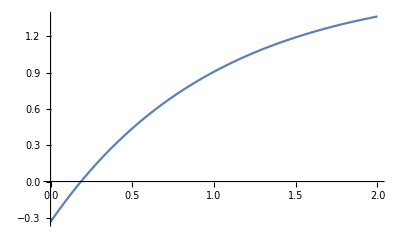

```mathematica
Plot[{Evaluate[Det[FMooe]/.{L->1, Aac->2, Eab->e,Eac->.2,Ebc->.2,V1a ->0.5,V1b->1.,V1c->1.5}],Evaluate[solooe[[1,3,2]]/Sin[Pi x/(2 L)]/ρC0/.{L->1, Aac->2, Eab->e,Eac->.2,Ebc->.2,V1a ->0.5,V1b->1.,V1c->1.5}]},{e,0,2}, PlotRange->Full]
```

Normalization:

```mathematica
∫_-1^1 (RhoA[x]+RhoB[x]+RhoC[x])ⅆx
```

ρ

So, ρ = 1.

```mathematica
ρ = 1;
```

### Export to python:

```mathematica
RhoA[x] /.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//FullSimplify
RhoB[x] /.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//FullSimplify
RhoC[x] /.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//Simplify
```

(expAB+expAC+expBC+(eta (-16 (-1+Aac) expAC expBC V1a+expAB^2 (16+32 Aac-4 (2 expAC+expBC+Aac expBC) per^2 pi^2+expAC expBC per^4 pi^4) signA V1a-8 (expAC+expBC) (-2 (2+Aac) expBC+expAC (-6+expBC per^2 pi^2)) signA V1a+16 (-1+Aac) expAC expBC V1b+expAB (8 expAC (8+4 Aac-expAC per^2 pi^2) signA V1a+expBC^2 per^2 pi^2 (-4-4 Aac+expAC per^2 pi^2) signA V1a+expBC (-16+(48+expAC per^2 pi^2 (-20+expAC per^2 pi^2)) signA+Aac (16+48 signA-4 expAC per^2 pi^2 signA)) V1a+32 (-1+Aac) expAC (V1b-V1c)-4 (-1+Aac) expBC (expAC per^2 pi^2 (V1b-V1c)+4 V1c))) Sin[(per pi x)/2])/(-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) per^2 pi^2-expAB expAC expBC per^4 pi^4))/(2 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC))

(Aac expAB+expAC+expBC+(eta (-16 (-1+Aac) expAC expBC V1a+16 (-1+Aac) expAC expBC V1b+Aac expAB^2 (16+32 Aac-4 (2 expAC+expBC+Aac expBC) per^2 pi^2+expAC expBC per^4 pi^4) signB V1b-8 (expAC+expBC) (-2 (2+Aac) expBC+expAC (-6+expBC per^2 pi^2)) signB V1b+expAB (expBC^2 per^2 pi^2 (-4-4 Aac+expAC per^2 pi^2) signB V1b+8 expAC ((2-2 Aac+2 signB+10 Aac signB-expAC per^2 pi^2 signB) V1b+2 (-1+Aac) V1c)+expBC (-4 (-1+Aac) (4+4 Aac-expAC per^2 pi^2) V1a+(16+16 Aac (4+Aac)-12 (1+Aac) expAC per^2 pi^2+expAC^2 per^4 pi^4) signB V1b+4 (-1+Aac) (4+4 Aac-expAC per^2 pi^2) V1c))) Sin[(per pi x)/2])/(-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) per^2 pi^2-expAB expAC expBC per^4 pi^4))/(2 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC))

(expAC+Aac (expAB+expBC)-(eta (-expAC (16 expAB V1b+48 expAC signC V1c-8 expAB (2+(-2+expAC per^2 pi^2) signC) V1c+expBC (-8+expAB per^2 pi^2) (4 V1a-4 V1b+(-4+expAC per^2 pi^2) signC V1c))+4 Aac^2 (-4 expBC^2 signC V1c+expAB^2 (-8+expBC per^2 pi^2) signC V1c+expAB expBC (-4 V1a+(4-12 signC+expBC per^2 pi^2 signC) V1c))-Aac (expAB^2 (16-4 expBC per^2 pi^2+expAC per^2 pi^2 (-8+expBC per^2 pi^2)) signC V1c+expAB (-4 expBC (4+expAC per^2 pi^2) V1a+expBC^2 per^2 pi^2 (-4+expAC per^2 pi^2) signC V1c+4 expAC expBC per^2 pi^2 (V1b-5 signC V1c)+16 expBC (V1c+3 signC V1c)+16 expAC (-V1b+V1c+5 signC V1c))-8 expBC (-4 expBC signC V1c+expAC (-4 V1a+4 V1b+(-8+expBC per^2 pi^2) signC V1c)))) Sin[(per pi x)/2])/(-8 (2 (2+Aac) expBC+expAC (6-expBC per^2 pi^2))+expAB (-16+8 expAC per^2 pi^2+4 expBC per^2 pi^2-expAC expBC per^4 pi^4+4 Aac (-8+expBC per^2 pi^2))))/(2 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC))

```mathematica
2 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)/.{Aac -> 3., expAB -> Exp[0.2], expBC -> Exp[0.5], expAC ->Exp[0.5]}
```

43.4792

```mathematica
(-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) π^2-expAB expAC expBC π^4)/.{Aac -> 3., expAB -> Exp[0.2], expBC -> Exp[0.5], expAC ->Exp[0.5]}
```

20.3825

```mathematica
-16 (-1+Aac) expAC expBC V1a+expAB^2 (16+32 Aac-4 (2 expAC+expBC+Aac expBC) π^2+expAC expBC π^4) signA V1a-8 (expAC+expBC) (-2 (2+Aac) expBC+expAC (-6+expBC π^2)) signA V1a+16 (-1+Aac) expAC expBC V1b+expAB (8 expAC (8+4 Aac-expAC π^2) signA V1a+expBC^2 π^2 (-4-4 Aac+expAC π^2) signA V1a+expBC (-16+(48+expAC π^2 (-20+expAC π^2)) signA+Aac (16+48 signA-4 expAC π^2 signA)) V1a+32 (-1+Aac) expAC (V1b-V1c)-4 (-1+Aac) expBC (expAC π^2 (V1b-V1c)+4 V1c))/.{Aac -> 3., expAB -> Exp[0.2], expBC -> Exp[0.5], expAC ->Exp[0.5], signA -> 1, signB -> 1, signC ->-1, V1a -> 0.5, V1b -> 1., V1c -> 1.5}
```

-0.367495

```mathematica
-16 (-1+Aac) expAC expBC V1a+16 (-1+Aac) expAC expBC V1b+Aac expAB^2 (16+32 Aac-4 (2 expAC+expBC+Aac expBC) π^2+expAC expBC π^4) signB V1b-8 (expAC+expBC) (-2 (2+Aac) expBC+expAC (-6+expBC π^2)) signB V1b+expAB (expBC^2 π^2 (-4-4 Aac+expAC π^2) signB V1b+8 expAC ((2-2 Aac+2 signB+10 Aac signB-expAC π^2 signB) V1b+2 (-1+Aac) V1c)+expBC (-4 (-1+Aac) (4+4 Aac-expAC π^2) V1a+(16+16 Aac (4+Aac)-12 (1+Aac) expAC π^2+expAC^2 π^4) signB V1b+4 (-1+Aac) (4+4 Aac-expAC π^2) V1c))/.{Aac -> 3., expAB -> Exp[0.2], expBC -> Exp[0.5], expAC ->Exp[0.5], signA -> 1, signB -> 1, signC ->-1, V1a -> 0.5, V1b -> 1., V1c -> 1.5}
```

-70.5692

```mathematica
-expAC (16 expAB V1b+48 expAC signC V1c-8 expAB (2+(-2+expAC π^2) signC) V1c+expBC (-8+expAB π^2) (4 V1a-4 V1b+(-4+expAC π^2) signC V1c))+4 Aac^2 (-4 expBC^2 signC V1c+expAB^2 (-8+expBC π^2) signC V1c+expAB expBC (-4 V1a+(4-12 signC+expBC π^2 signC) V1c))-Aac (expAB^2 (16-4 expBC π^2+expAC π^2 (-8+expBC π^2)) signC V1c+expAB (-4 expBC (4+expAC π^2) V1a+expBC^2 π^2 (-4+expAC π^2) signC V1c+4 expAC expBC π^2 (V1b-5 signC V1c)+16 expBC (V1c+3 signC V1c)+16 expAC (-V1b+V1c+5 signC V1c))-8 expBC (-4 expBC signC V1c+expAC (-4 V1a+4 V1b+(-8+expBC π^2) signC V1c)))/.{Aac -> 3., expAB -> Exp[0.2], expBC -> Exp[0.5], expAC ->Exp[0.5], signA -> 1, signB -> 1, signC ->-1, V1a -> 0.5, V1b -> 1., V1c -> 1.5}
```

-196.647

### Studying the solutions in equilibrium:

```mathematica
RhoA[x]//FullSimplify
```

1/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc))(ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc-((16 (1+2 Aac) ⅇ^(2 Eab) L^4 signA V1a+48 ⅇ^(2 Eac) L^4 signA V1a+16 (2+Aac) ⅇ^(2 Ebc) L^4 signA V1a-8 ⅇ^(2 Eab+Eac) L^2 per^2 π^2 signA V1a-8 ⅇ^(Eab+2 Eac) L^2 per^2 π^2 signA V1a-4 (1+Aac) ⅇ^(2 Eab+Ebc) L^2 per^2 π^2 signA V1a-8 ⅇ^(2 Eac+Ebc) L^2 per^2 π^2 signA V1a-4 (1+Aac) ⅇ^(Eab+2 Ebc) L^2 per^2 π^2 signA V1a-8 ⅇ^(Eac+2 Ebc) L^2 per^2 π^2 signA V1a+ⅇ^(2 Eab+Eac+Ebc) per^4 π^4 signA V1a+ⅇ^(Eab+2 Eac+Ebc) per^4 π^4 signA V1a+ⅇ^(Eab+Eac+2 Ebc) per^4 π^4 signA V1a+16 ⅇ^(Eac+Ebc) L^4 (V1a-Aac V1a+(5+Aac) signA V1a+(-1+Aac) V1b)+32 ⅇ^(Eab+Eac) L^4 ((2+Aac) signA V1a+(-1+Aac) (V1b-V1c))-4 ⅇ^(Eab+Eac+Ebc) L^2 per^2 π^2 ((5+Aac) signA V1a+(-1+Aac) (V1b-V1c))+16 ⅇ^(Eab+Ebc) L^4 ((-1+Aac+3 (1+Aac) signA) V1a+V1c-Aac V1c)) η Sin[(per π x)/(2 L)])/(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) L^2 per^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) L^2 per^2 π^2+ⅇ^(Eab+Eac) per^4 π^4)))

### Stat Phys solution:

```mathematica
Clear[ρAdiff, ρBdiff,ρCdiff]
```

```mathematica
ρAdiff[x_] =  Exp[-η V1a* Sin[(Pi x)/2]]
ρBdiff[x_] =  Exp[-η V1b  Sin[(Pi x)/2]]
ρCdiff[x_] =  Exp[-η V1c  Sin[(Pi x)/2]]
```

ⅇ^(-V1a η Sin[(π x)/2])

ⅇ^(-V1b η Sin[(π x)/2])

ⅇ^(-V1c η Sin[(π x)/2])

```mathematica
Z = Integrate[ρAdiff[x]+ρBdiff[x]+ρCdiff[x],{x,-1,1}]
```

2 (BesselI[0,V1a η]+BesselI[0,V1b η]+BesselI[0,V1c η])

```mathematica
rhoAdiff[x] = ρAdiff[x]/Z
rhoBdiff[x] = ρBdiff[x]/Z
rhoCdiff[x] = ρCdiff[x]/Z
```

ⅇ^(-V1a η Sin[(π x)/2])/(2 (BesselI[0,V1a η]+BesselI[0,V1b η]+BesselI[0,V1c η]))

ⅇ^(-V1b η Sin[(π x)/2])/(2 (BesselI[0,V1a η]+BesselI[0,V1b η]+BesselI[0,V1c η]))

ⅇ^(-V1c η Sin[(π x)/2])/(2 (BesselI[0,V1a η]+BesselI[0,V1b η]+BesselI[0,V1c η]))

```mathematica
Normal[Series[rhoAdiff[x],{η,0,1}]]
```

1/6-1/6 V1a η Sin[(π x)/2]

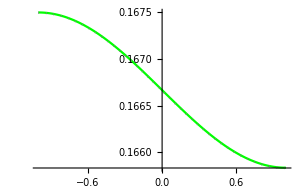

```mathematica
Plot[{Evaluate[RhoA[x]/. {Eab ->.2,Eac -> .2,Ebc -> .2, L ->1,V1a ->0.5,V1b ->1,V1c ->1.5, Aac -> 1., η -> 0.01, signA -> 1, signB -> 1, signC -> 1, per ->1}],Evaluate[rhoAdiff[x]/.{Eab ->.2,Eac -> .2,Ebc -> .2, L ->1,V1a ->0.5,V1b ->1,V1c ->1.5, Aac -> 1., η -> 0.01}]},{x,-1,1}, PlotStyle ->{Green, {Gray, Dotted}}]
```

```mathematica
(*Compatible with stat mech within the expansion*)
```

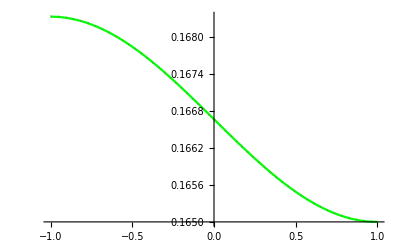

```mathematica
Plot[{Evaluate[RhoB[x]/. {Eab ->.2,Eac -> .2,Ebc -> .193, L ->1,V1a ->0.5,V1b ->1,V1c ->1.5, Aac -> 1., η -> 0.01, signA -> 1, signB -> 1, signC -> 1, per -> 1}],Evaluate[rhoBdiff[x]/.{Eab ->.2,Eac -> .2,Ebc -> .193, L ->1,V1a ->0.5,V1b ->1,V1c ->1.5, Aac -> 1., η -> 0.01}]},{x,-1,1}, PlotStyle ->{Green, {Gray, Dotted}}]
```

Quality of fit depends on whether α*η small enough.

### Parameter space in which expansion works:

I am plotting (ρ0-ρ)/ρ0, which should be close to 0 if the perturbed ρ is still close to the zero-order solution and hence the perturbative expansion makes sense.

Scales with α*η, so constant for all η .

```mathematica
DensityPlot[1-Evaluate[RhoA[1]/. {d ->1,ϵAB ->2.,ϵBC -> 3.,ϵAC -> 4., L ->1,αA ->0.5/0.01,αB ->par2/0.01,αC ->par1/0.01, μ -> 1.5, η -> 0.01}]/Evaluate[ρA0/. {ϵAB ->2.,ϵBC -> 3.,ϵAC -> 4., L ->1, μ ->1.5}],{par1,0,20},{par2,0,20}, PlotLegends->Automatic]
```

-Graphics-

ρA is super insensitive to 2 energies and very sensitive to one, which is αA.

Potential*η always has to be of the order of 0.1-0.01.

Barely changes with mu.

Barriers do not matter too much if the energies and η are chosen correctly.

```mathematica
Plot[Evaluate[RhoA[1]/.{L->1, ϵAB ->1,ϵBC ->1, ϵAC ->1,αA -> 10, αB -> 10, αC -> 10, η -> 0.001,μ -> mu}],{mu,0,10}, PlotRange->Full]
```

-Graphics-

How ρ scales with μ .

```mathematica
Plot[Evaluate[RhoA[1]/.{d ->1, L->1, ϵAB ->eps,ϵBC ->1, ϵAC ->1,αA -> 10, αB -> 10, αC -> 10, η -> 0.001,μ -> 4.}],{eps,0,10}, PlotRange->Full]
```

-Graphics-

There is a maximal value of ρ with ϵAB.

### Find the fluxes:

```mathematica
diffFluxA[x_] = D[RhoA[x],{x,1}]+ρA0 D[Va[x],{x,1}]//Simplify
```

((-1+Aac) f L π (4 ⅇ^(Eac+Ebc) L^2 (V1a-V1b)-4 ⅇ^(Eab+Ebc) L^2 (V1a-V1c)-8 ⅇ^(Eab+Eac) L^2 (V1b-V1c)+ⅇ^(Eab+Eac+Ebc) f^2 π^2 (V1b-V1c)) η Cos[(f π x)/(2 L)])/(((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4+16 (2+Aac) ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2-4 (1+Aac) ⅇ^(Eab+Ebc) f^2 L^2 π^2-8 ⅇ^(Eac+Ebc) f^2 L^2 π^2+ⅇ^(Eab+Eac+Ebc) f^4 π^4))

```mathematica
diffFluxB[x_] = D[RhoB[x],{x,1}]+ρB0 D[Vb[x],{x,1}]//Simplify
```

((-1+Aac) f L π (4 ⅇ^(Eac+Ebc) L^2 (V1a-V1b)+4 (1+Aac) ⅇ^(Eab+Ebc) L^2 (V1a-V1c)-ⅇ^(Eab+Eac+Ebc) f^2 π^2 (V1a-V1c)+4 ⅇ^(Eab+Eac) L^2 (V1b-V1c)) η Cos[(f π x)/(2 L)])/(((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4+16 (2+Aac) ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2-4 (1+Aac) ⅇ^(Eab+Ebc) f^2 L^2 π^2-8 ⅇ^(Eac+Ebc) f^2 L^2 π^2+ⅇ^(Eab+Eac+Ebc) f^4 π^4))

```mathematica
diffFluxC[x_] = D[RhoC[x],{x,1}]+ρC0 D[Vc[x],{x,1}]//FullSimplify
```

((-1+Aac) f L π (-8 ⅇ^(Eac+Ebc) L^2 (V1a-V1b)+ⅇ^(Eab+Eac) (ⅇ^Ebc f^2 π^2 (V1a-V1b)+4 L^2 (V1b-V1c))-4 Aac ⅇ^(Eab+Ebc) L^2 (V1a-V1c)) η Cos[(f π x)/(2 L)])/(((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) f^2 L^2 π^2+ⅇ^(Eab+Eac) f^4 π^4)))

The second summand:

```mathematica
ρA0 D[Va[x],{x,1}]/.{signA -> 1, signB ->1, signC -> 1, Aac -> μ, Eab -> Log[ab], Ebc -> Log[bc], Eac -> Log[ac]}//Simplify
```

((ab+ac+bc) f π V1a η Cos[(f π x)/(2 L)])/(4 L (ab+3 ac+2 ab μ+bc (2+μ)))

Showing that the derivative works:

```mathematica
D[RhoA[x],x]-f π η/(2L)*solooe[[1,1,2]]/Sin[(f π x)/(2 L)]*Cos[(f π x)/(2 L)]//FullSimplify
```

0

I am recovering the same result for the flux using not the full rho but only rho1 in the derivative (as it should be):

```mathematica
f π η/(2L)*solooe[[1,1,2]]/Sin[(f π x)/(2 L)]+((ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) f π signA V1a η)/(4 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) L)/.{signA -> 1, signB ->1, signC -> 1, Aac -> μ, Eab -> Log[ab], Ebc -> Log[bc], Eac -> Log[ac]}//FullSimplify
```

(f L π (4 ac bc L^2 (V1a-V1b)+ab (ac bc f^2 π^2 (V1b-V1c)+4 bc L^2 (-V1a+V1c)+8 ac L^2 (-V1b+V1c))) η (-1+μ))/((ab+3 ac+2 ab μ+bc (2+μ)) (ab ac bc f^4 π^4+8 ac L^2 (6 L^2-bc f^2 π^2)+16 bc L^4 (2+μ)+16 ab L^4 (1+2 μ)-4 ab f^2 L^2 π^2 (2 ac+bc+bc μ)))

The structure of drho/dx (without the cosine):

```mathematica
f π η/(2L)*solooe[[1,1,2]]/Sin[(f π x)/(2 L)]*(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) L^2 f^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) L^2 f^2 π^2+ⅇ^(Eab+Eac) f^4 π^4))/.{signA -> 1, signB ->1, signC -> 1, Aac -> μ, Eab -> Log[ab], Ebc -> Log[bc], Eac -> Log[ac]}//FullSimplify
```

-1/(4 L (ab+3 ac+2 ab μ+bc (2+μ)))f π η (8 L^2 (ac^2 (6 L^2-bc f^2 π^2) V1a+ac bc (-bc f^2 π^2 V1a+2 L^2 (6 V1a+V1b (-1+μ)))+2 bc^2 L^2 V1a (2+μ))+ab^2 V1a (ac bc f^4 π^4+16 L^4 (1+2 μ)-4 f^2 L^2 π^2 (2 ac+bc+bc μ))+ab (ac^2 f^2 π^2 (-8 L^2+bc f^2 π^2) V1a-4 bc L^2 (bc f^2 π^2 V1a (1+μ)-4 L^2 (2 V1a+V1c+4 V1a μ-V1c μ))+ac (bc^2 f^4 π^4 V1a+32 L^4 ((V1b-V1c) (-1+μ)+V1a (2+μ))-4 bc f^2 L^2 π^2 ((V1b-V1c) (-1+μ)+V1a (5+μ)))))

ρ0*dV/dx*denumerator of dρ1/dx has terms of f^4:

```mathematica
(ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) f π signA V1a η *(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) L^2 f^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) L^2 f^2 π^2+ⅇ^(Eab+Eac) f^4 π^4))/.{signA -> 1, signB ->1, signC -> 1, Aac -> μ, Eab -> Log[ab], Ebc -> Log[bc], Eac -> Log[ac]}//FullSimplify
```

(ab+ac+bc) f π V1a η (48 ac L^4-8 ab ac f^2 L^2 π^2+16 ab L^4 (1+2 μ)+bc (ab ac f^4 π^4+16 L^4 (2+μ)-4 f^2 L^2 π^2 (ab+2 ac+ab μ)))

```mathematica
D[solooe[[1,1,2]]/Sin[(f π x)/(2 L)],x]//FullSimplify
```

0

```mathematica
diffFluxA[x] /. Aac -> 1 //Simplify
diffFluxB[x] /. Aac -> 1 //Simplify
diffFluxC[x] /. Aac -> 1 //Simplify
```

0

0

0

```mathematica
(*Great*)
```

```mathematica
diffFluxA[x]+ diffFluxB[x]+diffFluxC[x]//FullSimplify
```

0

```mathematica
(*even greater*)
```

```mathematica
ExpandDenominator[ExpandNumerator[D[RhoA[x],{x,1}]]]/.{Aac -> μ, V1a-V1c -> Vac, V1a-V1b -> Vab, V1b-V1c -> Vbc, Eab -> Log[ab], Ebc -> Log[bc], Eac -> Log[ac]}//TraditionalForm
```

(-ab ac bc^2 π^5 signA V1a η cos((f π x)/(2 L)) f^5-ab ac^2 bc π^5 signA V1a η cos((f π x)/(2 L)) f^5-ab^2 ac bc π^5 signA V1a η cos((f π x)/(2 L)) f^5+8 ab ac^2 L^2 π^3 signA V1a η cos((f π x)/(2 L)) f^3+4 ab bc^2 L^2 π^3 signA V1a η cos((f π x)/(2 L)) f^3+8 ac bc^2 L^2 π^3 signA V1a η cos((f π x)/(2 L)) f^3+8 ab^2 ac L^2 π^3 signA V1a η cos((f π x)/(2 L)) f^3+4 ab^2 bc L^2 π^3 signA V1a η cos((f π x)/(2 L)) f^3+8 ac^2 bc L^2 π^3 signA V1a η cos((f π x)/(2 L)) f^3+20 ab ac bc L^2 π^3 signA V1a η cos((f π x)/(2 L)) f^3-4 ab ac bc L^2 π^3 V1b η cos((f π x)/(2 L)) f^3+4 ab ac bc L^2 π^3 V1c η cos((f π x)/(2 L)) f^3+4 ab bc^2 L^2 π^3 signA V1a η μ cos((f π x)/(2 L)) f^3+4 ab^2 bc L^2 π^3 signA V1a η μ cos((f π x)/(2 L)) f^3+4 ab ac bc L^2 π^3 signA V1a η μ cos((f π x)/(2 L)) f^3+4 ab ac bc L^2 π^3 V1b η μ cos((f π x)/(2 L)) f^3-4 ab ac bc L^2 π^3 V1c η μ cos((f π x)/(2 L)) f^3-16 ab^2 L^4 π signA V1a η cos((f π x)/(2 L)) f-48 ac^2 L^4 π signA V1a η cos((f π x)/(2 L)) f-32 bc^2 L^4 π signA V1a η cos((f π x)/(2 L)) f-64 ab ac L^4 π signA V1a η cos((f π x)/(2 L)) f-48 ab bc L^4 π signA V1a η cos((f π x)/(2 L)) f-80 ac bc L^4 π signA V1a η cos((f π x)/(2 L)) f+16 ab bc L^4 π V1a η cos((f π x)/(2 L)) f-16 ac bc L^4 π V1a η cos((f π x)/(2 L)) f+32 ab ac L^4 π V1b η cos((f π x)/(2 L)) f+16 ac bc L^4 π V1b η cos((f π x)/(2 L)) f-32 ab ac L^4 π V1c η cos((f π x)/(2 L)) f-16 ab bc L^4 π V1c η cos((f π x)/(2 L)) f-32 ab^2 L^4 π signA V1a η μ cos((f π x)/(2 L)) f-16 bc^2 L^4 π signA V1a η μ cos((f π x)/(2 L)) f-32 ab ac L^4 π signA V1a η μ cos((f π x)/(2 L)) f-48 ab bc L^4 π signA V1a η μ cos((f π x)/(2 L)) f-16 ac bc L^4 π signA V1a η μ cos((f π x)/(2 L)) f-16 ab bc L^4 π V1a η μ cos((f π x)/(2 L)) f+16 ac bc L^4 π V1a η μ cos((f π x)/(2 L)) f-32 ab ac L^4 π V1b η μ cos((f π x)/(2 L)) f-16 ac bc L^4 π V1b η μ cos((f π x)/(2 L)) f+32 ab ac L^4 π V1c η μ cos((f π x)/(2 L)) f+16 ab bc L^4 π V1c η μ cos((f π x)/(2 L)) f)/(64 ab^2 L^5+576 ac^2 L^5+256 bc^2 L^5+256 ab^2 μ^2 L^5+64 bc^2 μ^2 L^5+256 ab bc μ^2 L^5+384 ab ac L^5+256 ab bc L^5+768 ac bc L^5+256 ab^2 μ L^5+256 bc^2 μ L^5+768 ab ac μ L^5+640 ab bc μ L^5+384 ac bc μ L^5-16 ab bc^2 f^2 π^2 μ^2 L^3-32 ab^2 bc f^2 π^2 μ^2 L^3-48 ab bc^2 f^2 π^2 μ L^3-32 ac bc^2 f^2 π^2 μ L^3-64 ab^2 ac f^2 π^2 μ L^3-48 ab^2 bc f^2 π^2 μ L^3-144 ab ac bc f^2 π^2 μ L^3-96 ab ac^2 f^2 π^2 L^3-32 ab bc^2 f^2 π^2 L^3-64 ac bc^2 f^2 π^2 L^3-32 ab^2 ac f^2 π^2 L^3-16 ab^2 bc f^2 π^2 L^3-96 ac^2 bc f^2 π^2 L^3-144 ab ac bc f^2 π^2 L^3+4 ab ac bc^2 f^4 π^4 μ L+8 ab^2 ac bc f^4 π^4 μ L+8 ab ac bc^2 f^4 π^4 L+12 ab ac^2 bc f^4 π^4 L+4 ab^2 ac bc f^4 π^4 L)

```mathematica
rhoA0*D[Va[x],x]
```

((ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) f π signA V1a η Cos[(f π x)/(2 L)])/(4 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) L)

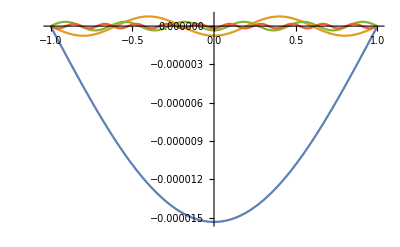

```mathematica
Plot[{diffFluxA[x]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.5,Eab -> 0.5, Ebc ->0.7,Eac -> 1., signA -> 1, signB ->1, signC ->1, f->1},diffFluxA[x]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.5,Eab -> 0.5, Ebc ->0.7,Eac -> 1., signA -> 1, signB ->1, signC ->1, f->5},
diffFluxA[x]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.5,Eab -> 0.5, Ebc ->0.7,Eac -> 1., signA -> 1, signB ->1, signC ->1, f->11},
diffFluxA[x]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.5,Eab -> 0.5, Ebc ->0.7,Eac -> 1., signA -> 1, signB ->1, signC ->1, f->21}},{x,-1,1}]
```

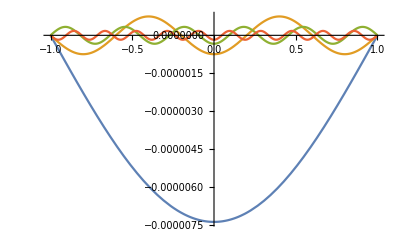

```mathematica
Plot[{diffFluxC[x]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.5,Eab -> 0.5, Ebc ->0.7,Eac -> 1., signA -> 1, signB ->1, signC ->1, f->1},diffFluxC[x]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.5,Eab -> 0.5, Ebc ->0.7,Eac -> 1., signA -> 1, signB ->1, signC ->1, f->5},
diffFluxC[x]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.5,Eab -> 0.5, Ebc ->0.7,Eac -> 1., signA -> 1, signB ->1, signC ->1, f->11},
diffFluxC[x]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.5,Eab -> 0.5, Ebc ->0.7,Eac -> 1., signA -> 1, signB ->1, signC ->1, f->21}},{x,-1,1}]
```

```mathematica
diffFluxA[0]
```

((-1+Aac) f L π (4 ⅇ^(Eac+Ebc) L^2 (V1a-V1b)-4 ⅇ^(Eab+Ebc) L^2 (V1a-V1c)-8 ⅇ^(Eab+Eac) L^2 (V1b-V1c)+ⅇ^(Eab+Eac+Ebc) f^2 π^2 (V1b-V1c)) η)/(((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4+16 (2+Aac) ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2-4 (1+Aac) ⅇ^(Eab+Ebc) f^2 L^2 π^2-8 ⅇ^(Eac+Ebc) f^2 L^2 π^2+ⅇ^(Eab+Eac+Ebc) f^4 π^4))

Ou fuck.

```mathematica
D[Va[x],{x,1}]//Simplify
```

(f π signA V1a η Cos[(f π x)/(2 L)])/(2 L)

```mathematica
D[Vb[x],{x,1}]//Simplify
```

(f π signB V1b η Cos[(f π x)/(2 L)])/(2 L)

```mathematica
D[Vc[x],{x,1}]//Simplify
```

(f π signC V1c η Cos[(f π x)/(2 L)])/(2 L)

```mathematica
D[RhoA[x],{x,1}]/.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//FullSimplify
D[RhoB[x],{x,1}]/.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//FullSimplify 
D[RhoC[x],{x,1}]/.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//FullSimplify
```

(eta pi (-16 (-1+Aac) expAC expBC V1a+expAB^2 (16+32 Aac-4 (2 expAC+expBC+Aac expBC) pi^2+expAC expBC pi^4) signA V1a-8 (expAC+expBC) (-2 (2+Aac) expBC+expAC (-6+expBC pi^2)) signA V1a+16 (-1+Aac) expAC expBC V1b+expAB (8 expAC (8+4 Aac-expAC pi^2) signA V1a+expBC^2 pi^2 (-4-4 Aac+expAC pi^2) signA V1a+expBC (-16+(48+expAC pi^2 (-20+expAC pi^2)) signA+Aac (16+48 signA-4 expAC pi^2 signA)) V1a+32 (-1+Aac) expAC (V1b-V1c)-4 (-1+Aac) expBC (expAC pi^2 (V1b-V1c)+4 V1c))) Cos[(pi x)/2])/(4 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC) (-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) pi^2-expAB expAC expBC pi^4))

(eta pi (-16 (-1+Aac) expAC expBC V1a+16 (-1+Aac) expAC expBC V1b+Aac expAB^2 (16+32 Aac-4 (2 expAC+expBC+Aac expBC) pi^2+expAC expBC pi^4) signB V1b-8 (expAC+expBC) (-2 (2+Aac) expBC+expAC (-6+expBC pi^2)) signB V1b+expAB (expBC^2 pi^2 (-4-4 Aac+expAC pi^2) signB V1b+8 expAC ((2-2 Aac+2 signB+10 Aac signB-expAC pi^2 signB) V1b+2 (-1+Aac) V1c)+expBC (-4 (-1+Aac) (4+4 Aac-expAC pi^2) V1a+(16+16 Aac (4+Aac)-12 (1+Aac) expAC pi^2+expAC^2 pi^4) signB V1b+4 (-1+Aac) (4+4 Aac-expAC pi^2) V1c))) Cos[(pi x)/2])/(4 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC) (-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) pi^2-expAB expAC expBC pi^4))

(eta pi (4 (-1+Aac) (4 Aac expAB expBC V1a-expAC expBC (-8+expAB pi^2) (V1a-V1b)-4 expAB expAC V1b)+(-16 (-1+Aac) expAB (-expAC+Aac expBC)-(expAC+Aac (expAB+expBC)) (-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) pi^2-expAB expAC expBC pi^4) signC) V1c) Cos[(pi x)/2])/(4 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC) (-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) pi^2-expAB expAC expBC pi^4))

Export to python:

```mathematica
diffFluxA[x]/.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//FullSimplify
diffFluxB[x]/.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//FullSimplify
diffFluxC[x]/.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//FullSimplify
diffFluxCalt[x]/.{L ->1, η -> eta, Eab -> Log[expAB],Ebc -> Log[expBC],Eac -> Log[expAC], π -> pi}//FullSimplify
```

((-1+Aac) eta per pi (4 expAC expBC (-V1a+V1b)+8 expAB expAC (V1b-V1c)+expAB expBC (4 V1a-4 V1c+expAC per^2 pi^2 (-V1b+V1c))) Cos[(per pi x)/2])/((expAB+2 Aac expAB+3 expAC+(2+Aac) expBC) (-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) per^2 pi^2-expAB expAC expBC per^4 pi^4))

-(((-1+Aac) eta per pi (4 expAC expBC (V1a-V1b)+expAB expBC (4+4 Aac-expAC per^2 pi^2) (V1a-V1c)+4 expAB expAC (V1b-V1c)) Cos[(per pi x)/2])/((expAB+2 Aac expAB+3 expAC+(2+Aac) expBC) (-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) per^2 pi^2-expAB expAC expBC per^4 pi^4)))

((-1+Aac) eta per pi (-expAC expBC (-8+expAB per^2 pi^2) (V1a-V1b)+4 Aac expAB expBC (V1a-V1c)+4 expAB expAC (-V1b+V1c)) Cos[(per pi x)/2])/((expAB+2 Aac expAB+3 expAC+(2+Aac) expBC) (-16 (expAB+2 Aac expAB+3 expAC+(2+Aac) expBC)+4 (2 expAC expBC+expAB (2 expAC+expBC+Aac expBC)) per^2 pi^2-expAB expAC expBC per^4 pi^4))

diffFluxCalt[x]

```mathematica
diffFluxCalt[x_] = D[RhoC[x],{x,1}]+RhoC[x]* D[Vc[x],{x,1}]//FullSimplify
```

-((f π η Cos[(f π x)/(2 L)] (4 (-1+Aac) L^2 (8 ⅇ^(Eac+Ebc) L^2 (V1a-V1b)+4 Aac ⅇ^(Eab+Ebc) L^2 (V1a-V1c)+ⅇ^(Eab+Eac) (-ⅇ^Ebc f^2 π^2 (V1a-V1b)+4 L^2 (-V1b+V1c)))+signC V1c (4 Aac^2 L^2 (8 ⅇ^(2 Eab) L^2 signC V1c+ⅇ^(2 Ebc) (4 L^2-ⅇ^Eab f^2 π^2) signC V1c+ⅇ^(Eab+Ebc) (-ⅇ^Eab f^2 π^2 signC V1c+4 L^2 (V1a-V1c+3 signC V1c)))+4 Aac L^2 (4 ⅇ^(2 Eab) L^2 signC V1c+ⅇ^(2 Ebc) (8 L^2-ⅇ^Eab f^2 π^2) signC V1c+ⅇ^(Eab+Ebc) (-ⅇ^Eab f^2 π^2 signC V1c+4 L^2 (-V1a+V1c+3 signC V1c)))+Aac ⅇ^Eac (ⅇ^(2 Eab) f^2 π^2 (-8 L^2+ⅇ^Ebc f^2 π^2) signC V1c+8 ⅇ^Ebc L^2 (-ⅇ^Ebc f^2 π^2 signC V1c+4 L^2 (V1a-V1b+2 signC V1c))+ⅇ^Eab (ⅇ^(2 Ebc) f^4 π^4 signC V1c-4 ⅇ^Ebc f^2 L^2 π^2 (V1a-V1b+5 signC V1c)+16 L^4 (-V1b+V1c+5 signC V1c)))+ⅇ^Eac (8 ⅇ^Eac L^2 (6 L^2-ⅇ^Ebc f^2 π^2) signC V1c-32 ⅇ^Ebc L^4 (V1a-V1b-signC V1c)+ⅇ^Eab (-8 ⅇ^Eac f^2 L^2 π^2 signC V1c+16 L^4 (V1b+(-1+signC) V1c)+ⅇ^Ebc f^2 π^2 (ⅇ^Eac f^2 π^2 signC V1c-4 L^2 (-V1a+V1b+signC V1c))))) η Sin[(f π x)/(2 L)]))/(4 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) L (16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) f^2 L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) f^2 L^2 π^2+ⅇ^(Eab+Eac) f^4 π^4))))

### Small train aside

```mathematica
AacSing/.L->1
```

(-16 ⅇ^Eab-48 ⅇ^Eac-32 ⅇ^Ebc+8 ⅇ^(Eab+Eac) f^2 π^2+4 ⅇ^(Eab+Ebc) f^2 π^2+8 ⅇ^(Eac+Ebc) f^2 π^2-ⅇ^(Eab+Eac+Ebc) f^4 π^4)/(4 (8 ⅇ^Eab+4 ⅇ^Ebc-ⅇ^(Eab+Ebc) f^2 π^2))

```mathematica
Solve[(8 ⅇ^Eab+4 ⅇ^Ebc-ⅇ^(Eab+Ebc) f^2 π^2)==0,f]/.{Eab ->1, Ebc ->1, Eac ->1}
```

{{f→-(2 √(3/ⅇ))/π},{f→(2 √(3/ⅇ))/π}}

```mathematica
N[(2 √(3/ⅇ))/π]
```

0.668796

```mathematica
Solve[(8 ⅇ^Eab+4 ⅇ^Ebc-ⅇ^(Eab+Ebc) f^2 π^2)==0,Eab]/.{f ->1, Ebc ->1, Eac ->1}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Eab→1-Log[1/4 (-8+ⅇ π^2)]}}

```mathematica
N[1-Log[1/4 (-8+ⅇ π^2)]]
```

-0.54907

This is irrelevant.

```mathematica
fluxprefA[x_,f_,Eab_,Ebc_,Eac_, V1a_, V1b_, V1c_, η_]=((-1+Aac) L f π (4 ⅇ^(Eac+Ebc) L^2 (V1a-V1b)-4 ⅇ^(Eab+Ebc) L^2 (V1a-V1c)-8 ⅇ^(Eab+Eac) L^2 (V1b-V1c)+ⅇ^(Eab+Eac+Ebc) f^2 π^2 (V1b-V1c)) η )/(((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4+16 (2+Aac) ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) L^2 f^2 π^2-4 (1+Aac) ⅇ^(Eab+Ebc) L^2 f^2 π^2-8 ⅇ^(Eac+Ebc) L^2 f^2 π^2+ⅇ^(Eab+Eac+Ebc) f^4 π^4))/.{Aac->AacSing+x}/.L->1//Simplify
```

-(f π (4 ⅇ^(Eac+Ebc) (V1a-V1b)-4 ⅇ^(Eab+Ebc) (V1a-V1c)-8 ⅇ^(Eab+Eac) (V1b-V1c)+ⅇ^(Eab+Eac+Ebc) f^2 π^2 (V1b-V1c)) (48 ⅇ^Eac-8 ⅇ^(Eab+Eac) f^2 π^2-8 ⅇ^(Eac+Ebc) f^2 π^2+ⅇ^(Eab+Eac+Ebc) f^4 π^4+ⅇ^Eab (48-32 x)-16 ⅇ^Ebc (-3+x)+4 ⅇ^(Eab+Ebc) f^2 π^2 (-2+x)) η)/(4 (-8 ⅇ^Eab-4 ⅇ^Ebc+ⅇ^(Eab+Ebc) f^2 π^2) x (-16 ⅇ^(2 Eab+Eac) f^2 π^2-12 ⅇ^(Eab+Eac+Ebc) f^2 π^2-8 ⅇ^(Eac+2 Ebc) f^2 π^2+2 ⅇ^(2 Eab+Eac+Ebc) f^4 π^4+ⅇ^(Eab+Eac+2 Ebc) f^4 π^4-64 ⅇ^(2 Eab) x-16 ⅇ^(2 Ebc) x-64 ⅇ^(Eab+Ebc) x+4 ⅇ^(Eab+2 Ebc) f^2 π^2 (1+x)+4 ⅇ^(2 Eab+Ebc) f^2 π^2 (-1+2 x)))

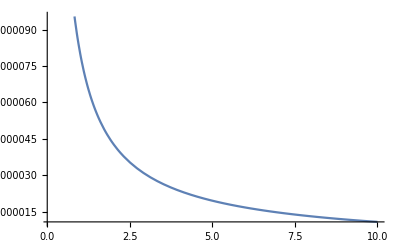

```mathematica
Plot[fluxprefA[par,1,1,1,1,0.5,1,1.5,0.001],{par,0.1,10}]
```

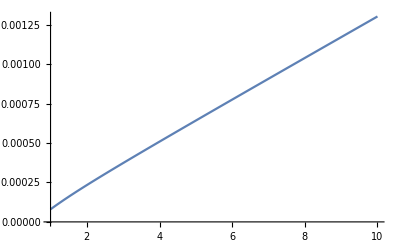

```mathematica
Plot[fluxprefA[1,freq,1,1,1,0.5,1,1.5,0.001],{freq,1,10}]
```

Wait, dafuq. The only thing I changed was saying that Aac = AacSing[per] + x. Apparently it drastically changes everything?

```mathematica
fluxprefA[x,per,Eab,Ebc,Eac, V1a, V1b, V1c, η]/.{Aac -> μ, V1a-V1c -> Vac, V1a-V1b -> Vab, V1b-V1c -> Vbc, Eab -> Log[ab], Ebc -> Log[bc], Eac -> Log[ac]}
```

-(per π (4 ac bc Vab-4 ab bc Vac-8 ab ac Vbc+ab ac bc per^2 π^2 Vbc) (48 ac-8 ab ac per^2 π^2-8 ac bc per^2 π^2+ab ac bc per^4 π^4+ab (48-32 x)-16 bc (-3+x)+4 ab bc per^2 π^2 (-2+x)) η)/(4 (-8 ab-4 bc+ab bc per^2 π^2) x (-16 ab^2 ac per^2 π^2-12 ab ac bc per^2 π^2-8 ac bc^2 per^2 π^2+2 ab^2 ac bc per^4 π^4+ab ac bc^2 per^4 π^4-64 ab^2 x-64 ab bc x-16 bc^2 x+4 ab bc^2 per^2 π^2 (1+x)+4 ab^2 bc per^2 π^2 (-1+2 x)))

```mathematica
ExpandDenominator[ExpandNumerator[fluxprefA[x,f,Eab,Ebc,Eac, V1a, V1b, V1c, η]]]/.{Aac -> μ, V1a-V1c -> Vac, V1a-V1b -> Vab, V1b-V1c -> Vbc, Eab -> Log[ab], Ebc -> Log[bc], Eac -> Log[ac]}//TraditionalForm
```

(-ab^2 ac^2 bc^2 π^7 V1b η f^7+ab^2 ac^2 bc^2 π^7 V1c η f^7-4 ab ac^2 bc^2 π^5 V1a η f^5+4 ab^2 ac bc^2 π^5 V1a η f^5+12 ab ac^2 bc^2 π^5 V1b η f^5+8 ab^2 ac bc^2 π^5 V1b η f^5+16 ab^2 ac^2 bc π^5 V1b η f^5-8 ab ac^2 bc^2 π^5 V1c η f^5-12 ab^2 ac bc^2 π^5 V1c η f^5-16 ab^2 ac^2 bc π^5 V1c η f^5-4 ab^2 ac bc^2 π^5 V1b x η f^5+4 ab^2 ac bc^2 π^5 V1c x η f^5-32 ab^2 bc^2 π^3 V1a η f^3+32 ac^2 bc^2 π^3 V1a η f^3+32 ab ac^2 bc π^3 V1a η f^3-32 ab^2 ac bc π^3 V1a η f^3-64 ab^2 ac^2 π^3 V1b η f^3-32 ac^2 bc^2 π^3 V1b η f^3-80 ab ac bc^2 π^3 V1b η f^3-144 ab ac^2 bc π^3 V1b η f^3-112 ab^2 ac bc π^3 V1b η f^3+64 ab^2 ac^2 π^3 V1c η f^3+32 ab^2 bc^2 π^3 V1c η f^3+80 ab ac bc^2 π^3 V1c η f^3+112 ab ac^2 bc π^3 V1c η f^3+144 ab^2 ac bc π^3 V1c η f^3+16 ab^2 bc^2 π^3 V1a x η f^3-16 ab ac bc^2 π^3 V1a x η f^3+32 ab ac bc^2 π^3 V1b x η f^3+64 ab^2 ac bc π^3 V1b x η f^3-16 ab^2 bc^2 π^3 V1c x η f^3-16 ab ac bc^2 π^3 V1c x η f^3-64 ab^2 ac bc π^3 V1c x η f^3+192 ab bc^2 π V1a η f-192 ac bc^2 π V1a η f+192 ab^2 bc π V1a η f-192 ac^2 bc π V1a η f+384 ab ac^2 π V1b η f+192 ac bc^2 π V1b η f+384 ab^2 ac π V1b η f+192 ac^2 bc π V1b η f+576 ab ac bc π V1b η f-384 ab ac^2 π V1c η f-192 ab bc^2 π V1c η f-384 ab^2 ac π V1c η f-192 ab^2 bc π V1c η f-576 ab ac bc π V1c η f-64 ab bc^2 π V1a x η f+64 ac bc^2 π V1a x η f-128 ab^2 bc π V1a x η f+128 ab ac bc π V1a x η f-64 ac bc^2 π V1b x η f-256 ab^2 ac π V1b x η f-256 ab ac bc π V1b x η f+64 ab bc^2 π V1c x η f+256 ab^2 ac π V1c x η f+128 ab^2 bc π V1c x η f+128 ab ac bc π V1c x η f)/(4 ab^2 ac bc^3 π^6 x f^6+8 ab^3 ac bc^2 π^6 x f^6+16 ab^2 bc^3 π^4 x^2 f^4+32 ab^3 bc^2 π^4 x^2 f^4+16 ab^2 bc^3 π^4 x f^4-48 ab ac bc^3 π^4 x f^4-16 ab^3 bc^2 π^4 x f^4-112 ab^2 ac bc^2 π^4 x f^4-128 ab^3 ac bc π^4 x f^4-128 ab bc^3 π^2 x^2 f^2-512 ab^2 bc^2 π^2 x^2 f^2-512 ab^3 bc π^2 x^2 f^2-64 ab bc^3 π^2 x f^2+128 ac bc^3 π^2 x f^2-64 ab^2 bc^2 π^2 x f^2+448 ab ac bc^2 π^2 x f^2+512 ab^3 ac π^2 x f^2+128 ab^3 bc π^2 x f^2+640 ab^2 ac bc π^2 x f^2+2048 ab^3 x^2+256 bc^3 x^2+1536 ab bc^2 x^2+3072 ab^2 bc x^2)

Why exactly is this so fucked?

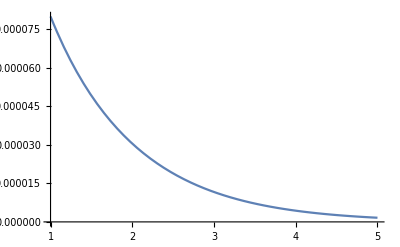

```mathematica
Plot[fluxprefA[1,1,par,1,1,0.5,1,1.5,0.001],{par,1,5}]
```

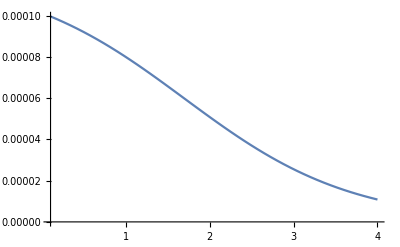

```mathematica
Plot[fluxprefA[1,1,1,par,1,0.5,1,1.5,0.001],{par,0.1,4}]
```

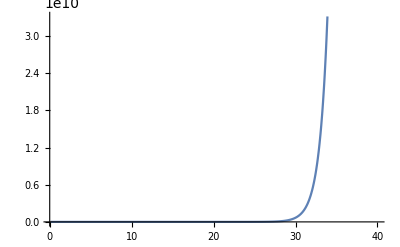

```mathematica
Plot[fluxprefA[1,1,1,1,par,0.5,1,1.5,0.001],{par,0.1,40}]
```

```mathematica
fluxprefA[x,f,Eab,Ebc,Eac, V1a, V1b, V1c, η]/.{Aac -> μ, V1a-V1c -> Vac, V1a-V1b -> Vab, V1b-V1c -> Vbc, Eab -> Log[ab], Ebc -> Log[bc], Eac -> Log[ac], L->1}
```

-(f π (4 ac bc Vab-4 ab bc Vac-8 ab ac Vbc+ab ac bc f^2 π^2 Vbc) (48 ac-8 ab ac f^2 π^2-8 ac bc f^2 π^2+ab ac bc f^4 π^4+ab (48-32 x)-16 bc (-3+x)+4 ab bc f^2 π^2 (-2+x)) η)/(4 (-8 ab-4 bc+ab bc f^2 π^2) x (-16 ab^2 ac f^2 π^2-12 ab ac bc f^2 π^2-8 ac bc^2 f^2 π^2+2 ab^2 ac bc f^4 π^4+ab ac bc^2 f^4 π^4-64 ab^2 x-64 ab bc x-16 bc^2 x+4 ab bc^2 f^2 π^2 (1+x)+4 ab^2 bc f^2 π^2 (-1+2 x)))

```mathematica
fluxprefA[1,1,1,1,Eac,0.5,1,1.5,0.001]
```

-(0.0000194851 (29.5562+2. ⅇ^(1+Eac)-4.9348 ⅇ^(2+Eac)) (48 ⅇ+48 ⅇ^Eac-4 ⅇ^2 π^2-16 ⅇ^(1+Eac) π^2+ⅇ^(2+Eac) π^4))/(-144 ⅇ^2+12 ⅇ^3 π^2-36 ⅇ^(2+Eac) π^2+3 ⅇ^(3+Eac) π^4)

```mathematica
Solve[-144 ⅇ^2+12 ⅇ^3 π^2-36 ⅇ^(2+Eac) π^2+3 ⅇ^(3+Eac) π^4==0,Eac]
```

{{Eac→ConditionalExpression[ⅈ π+2 ⅈ π C[1]+Log[-(144-12 ⅇ π^2)/(-36 π^2+3 ⅇ π^4)], C[1]∈ℤ]}}

hum. It’s just getting big because it genuinely gets big. It’s exponential and stuff. That’s nice?

```mathematica
Plot[-0.000019485075540335276 (29.5562243957226+2. ⅇ^(1+Eac)-4.934802200544679 ⅇ^(2+Eac)) (48 ⅇ+48 ⅇ^Eac-4 ⅇ^2 π^2-16 ⅇ^(1+Eac) π^2+ⅇ^(2+Eac) π^4),{Eac,0.1,40}]
```

-Graphics-

```mathematica
Plot[-144 ⅇ^2+12 ⅇ^3 π^2-36 ⅇ^(2+Eac) π^2+3 ⅇ^(3+Eac) π^4,{Eac,0.1,40}]
```

-Graphics-

I do not know if this should not happen.

```mathematica
Plot[fluxprefA[1,1,1,1,1,par,1,1.5,0.001],{par,0.1,50}]
```

-Graphics-

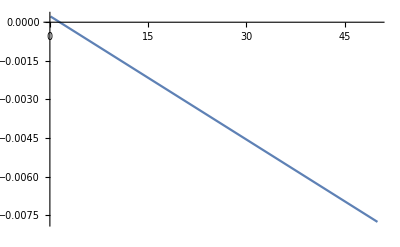

```mathematica
Plot[fluxprefA[1,1,1,1,1,0.5,par,1.5,0.001],{par,0.1,50}]
```

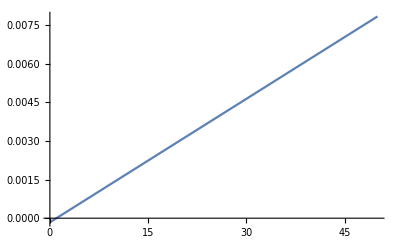

```mathematica
Plot[fluxprefA[1,1,1,1,1,0.5,1,par,0.001],{par,0.1,50}]
```

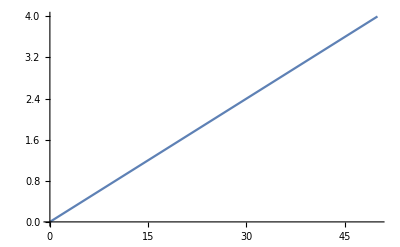

```mathematica
Plot[fluxprefA[1,1,1,1,1,0.5,1,1.5,par],{par,0.1,50}]
```

### Explore parameter space where fluxes are big (gish)

Avoid the parameter space where expansion breaks down!

```mathematica
AacSing
```

(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 per^2 π^2+4 ⅇ^(Eab+Ebc) L^2 per^2 π^2+8 ⅇ^(Eac+Ebc) L^2 per^2 π^2-ⅇ^(Eab+Eac+Ebc) per^4 π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) per^2 π^2))

Look at denominator of the fluxes (one for all):

```mathematica
Solve[((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4+16 (2+Aac) ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) L^2 per^2 π^2-4 (1+Aac) ⅇ^(Eab+Ebc) L^2 per^2 π^2-8 ⅇ^(Eac+Ebc) L^2 per^2 π^2+ⅇ^(Eab+Eac+Ebc) per^4 π^4)==0,Aac]
```

{{Aac→-(ⅇ^Eab+3 ⅇ^Eac+2 ⅇ^Ebc)/(2 ⅇ^Eab+ⅇ^Ebc)},{Aac→-(16 ⅇ^Eab L^4+48 ⅇ^Eac L^4+32 ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) L^2 per^2 π^2-4 ⅇ^(Eab+Ebc) L^2 per^2 π^2-8 ⅇ^(Eac+Ebc) L^2 per^2 π^2+ⅇ^(Eab+Eac+Ebc) per^4 π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) per^2 π^2))}}

One is the same. The other is always negative. Hence there are no other divergencies in the fluxes, theoretically.

```mathematica
Clear[diffFluxB1]
```

```mathematica
diffFluxB1[x_,Aac_,offset_] = If[AacSing < 0, Evaluate[diffFluxB[x]/.Aac],Evaluate[diffFluxB[x] /.Aac -> AacSing+offset]]
```

ReplaceAll::reps: {Aac} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

If[(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))<0,1/(4 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) L)π ((Aac ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) V1b-(16 Aac (1+2 Aac) ⅇ^(2 Eab) L^4 signB V1b+48 ⅇ^(2 Eac) L^4 signB V1b+16 (2+Aac) ⅇ^(2 Ebc) L^4 signB V1b-8 Aac ⅇ^(2 Eab+Eac) L^2 π^2 signB V1b-8 ⅇ^(Eab+2 Eac) L^2 π^2 signB V1b-4 Aac (1+Aac) ⅇ^(2 Eab+Ebc) L^2 π^2 signB V1b-8 ⅇ^(2 Eac+Ebc) L^2 π^2 signB V1b-4 (1+Aac) ⅇ^(Eab+2 Ebc) L^2 π^2 signB V1b-8 ⅇ^(Eac+2 Ebc) L^2 π^2 signB V1b+Aac ⅇ^(2 Eab+Eac+Ebc) π^4 signB V1b+ⅇ^(Eab+2 Eac+Ebc) π^4 signB V1b+ⅇ^(Eab+Eac+2 Ebc) π^4 signB V1b-16 ⅇ^(Eac+Ebc) L^4 ((-1+Aac) V1a+V1b-(Aac+(5+Aac) signB) V1b)+16 ⅇ^(Eab+Eac) L^4 ((1+signB+Aac (-1+5 signB)) V1b+(-1+Aac) V1c)+4 ⅇ^(Eab+Eac+Ebc) L^2 π^2 ((-1+Aac) V1a-3 (1+Aac) signB V1b+V1c-Aac V1c)-16 ⅇ^(Eab+Ebc) L^4 ((-1+Aac^2) V1a-(1+Aac (4+Aac)) signB V1b+V1c-Aac^2 V1c))/(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) L^2 π^2+ⅇ^(Eab+Eac) π^4))) η Cos[(π x)/(2 L)]/.Aac,(π ((ⅇ^Eac+ⅇ^Ebc+ⅇ^Eab (offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2)))) V1b-(48 ⅇ^(2 Eac) L^4 signB V1b-8 ⅇ^(Eab+2 Eac) L^2 π^2 signB V1b-8 ⅇ^(2 Eac+Ebc) L^2 π^2 signB V1b-8 ⅇ^(Eac+2 Ebc) L^2 π^2 signB V1b+ⅇ^(Eab+2 Eac+Ebc) π^4 signB V1b+ⅇ^(Eab+Eac+2 Ebc) π^4 signB V1b-8 ⅇ^(2 Eab+Eac) L^2 π^2 (offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) signB V1b+ⅇ^(2 Eab+Eac+Ebc) π^4 (offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) signB V1b-4 ⅇ^(Eab+2 Ebc) L^2 π^2 (1+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) signB V1b-4 ⅇ^(2 Eab+Ebc) L^2 π^2 (offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) (1+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) signB V1b+16 ⅇ^(2 Ebc) L^4 (2+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) signB V1b+16 ⅇ^(2 Eab) L^4 (offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) (1+2 (offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2)))) signB V1b-16 ⅇ^(Eac+Ebc) L^4 ((-1+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) V1a+V1b-(offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))+(5+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) signB) V1b)+16 ⅇ^(Eab+Eac) L^4 ((1+signB+(offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) (-1+5 signB)) V1b+(-1+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) V1c)+4 ⅇ^(Eab+Eac+Ebc) L^2 π^2 ((-1+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) V1a-3 (1+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) signB V1b+V1c-(offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) V1c)-16 ⅇ^(Eab+Ebc) L^4 ((-1+(offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2)))^2) V1a-(1+(offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))) (4+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2)))) signB V1b+V1c-(offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2)))^2 V1c))/(48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) L^2 π^2+16 ⅇ^Eab L^4 (1+2 (offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))))+ⅇ^Ebc (ⅇ^(Eab+Eac) π^4+16 L^4 (2+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2)))-4 L^2 π^2 (2 ⅇ^Eac+ⅇ^Eab (1+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))))))) η Cos[(π x)/(2 L)])/(4 L (3 ⅇ^Eac+ⅇ^Ebc (2+offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2)))+ⅇ^Eab (1+2 (offset+(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))))))]

```mathematica
Evaluate[diffFluxB1[0,1.6,muOffset] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Eab ->par1, Ebc ->par2,Eac -> 0.6}]
```

If[(-87.4617-16 ⅇ^par1-32 ⅇ^par2+8 ⅇ^(0.6+par1) π^2+8 ⅇ^(0.6+par2) π^2+4 ⅇ^(par1+par2) π^2-ⅇ^(0.6+par1+par2) π^4)/(4 (8 ⅇ^par1+4 ⅇ^par2-ⅇ^(par1+par2) π^2))<0,1/(4 ((1+2 1.6) ⅇ^par1+3 ⅇ^0.6+(2+1.6) ⅇ^par2))π ((1.6 ⅇ^par1+ⅇ^0.6+ⅇ^par2) 1-(16 1.6 (1+2 1.6) ⅇ^(2 par1) 1^4 signB+48 ⅇ^(2 0.6) 1^4 signB+16 (2+1.6) ⅇ^(2 par2) 1^4 signB-8 1.6 ⅇ^(2 par1+0.6) 1^2 π^2 signB-8 ⅇ^(par1+2 0.6) 1^2 π^2 signB-4 1.6 (1+1.6) ⅇ^(2 par1+par2) 1^2 π^2 signB-8 ⅇ^(2 0.6+par2) 1^2 π^2 signB-4 (1+1.6) ⅇ^(par1+2 par2) 1^2 π^2 signB-8 ⅇ^(0.6+2 par2) 1^2 π^2 signB+1.6 ⅇ^(2 par1+0.6+par2) π^4 signB+ⅇ^(par1+2 0.6+par2) π^4 signB+ⅇ^(par1+0.6+2 par2) π^4 signB-16 ⅇ^(0.6+par2) 1^4 ((-1+1.6) 0.5+1-(1.6+(5+1.6) signB) 1)+16 ⅇ^(par1+0.6) 1^4 ((1+signB+1.6 (-1+5 signB)) 1+(-1+1.6) 1.5)+4 ⅇ^(par1+0.6+par2) 1^2 π^2 ((-1+1.6) 0.5-3 (1+1.6) signB+1.5-1.6 1.5)-16 ⅇ^(par1+par2) 1^4 ((-1+1.6^2) 0.5-(1+1.6 (4+1.6)) signB+1.5-1.6^2 1.5))/(16 (1+2 1.6) ⅇ^par1 1^4+48 ⅇ^0.6 1^4-8 ⅇ^(par1+0.6) 1^2 π^2+ⅇ^par2 (16 (2+1.6) 1^4-4 ((1+1.6) ⅇ^par1+2 ⅇ^0.6) 1^2 π^2+ⅇ^(par1+0.6) π^4))) 0.01 Cos[(π 0)/2]/.1.6,(π ((ⅇ^0.6+ⅇ^par2+ⅇ^par1 (muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2)))) 1-(48 ⅇ^(2 0.6) 1^4 signB-8 ⅇ^(par1+2 0.6) 1^2 π^2 signB-8 ⅇ^(2 0.6+par2) 1^2 π^2 signB-8 ⅇ^(0.6+2 par2) 1^2 π^2 signB+ⅇ^(par1+2 0.6+par2) π^4 signB+ⅇ^(par1+0.6+2 par2) π^4 signB-8 ⅇ^(2 par1+0.6) 1^2 π^2 (muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) signB+ⅇ^(2 par1+0.6+par2) π^4 (muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) signB-4 ⅇ^(par1+2 par2) 1^2 π^2 (1+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) signB-4 ⅇ^(2 par1+par2) 1^2 π^2 (muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) (1+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) signB+16 ⅇ^(2 par2) 1^4 (2+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) signB+16 ⅇ^(2 par1) 1^4 (muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) (1+2 (muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2)))) signB-16 ⅇ^(0.6+par2) 1^4 ((-1+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) 0.5+1-(muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))+(5+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) signB) 1)+16 ⅇ^(par1+0.6) 1^4 ((1+signB+(muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) (-1+5 signB)) 1+(-1+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) 1.5)+4 ⅇ^(par1+0.6+par2) 1^2 π^2 ((-1+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) 0.5-3 (1+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) signB+1.5-(muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) 1.5)-16 ⅇ^(par1+par2) 1^4 ((-1+(muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2)))^2) 0.5-(1+(muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))) (4+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2)))) signB+1.5-(muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2)))^2 1.5))/(48 ⅇ^0.6 1^4-8 ⅇ^(par1+0.6) 1^2 π^2+16 ⅇ^par1 1^4 (1+2 (muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))))+ⅇ^par2 (ⅇ^(par1+0.6) π^4+16 1^4 (2+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2)))-4 1^2 π^2 (2 ⅇ^0.6+ⅇ^par1 (1+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))))))) 0.01 Cos[(π 0)/2])/(4 (3 ⅇ^0.6+ⅇ^par2 (2+muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2)))+ⅇ^par1 (1+2 (muOffset+(-16 ⅇ^par1 1^4-48 ⅇ^0.6 1^4-32 ⅇ^par2 1^4+8 ⅇ^(par1+0.6) 1^2 π^2+4 ⅇ^(par1+par2) 1^2 π^2+8 ⅇ^(0.6+par2) 1^2 π^2-ⅇ^(par1+0.6+par2) π^4)/(4 1^2 (8 ⅇ^par1 1^2+4 ⅇ^par2 1^2-ⅇ^(par1+par2) π^2))))))]

```mathematica
ContourPlot[Evaluate[diffFluxB[0] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac->1.6,Eab ->par1, Ebc ->par2,Eac -> 0.6}],{par1,0.00001,1},{par2,0.00001,1},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

What the major.

```mathematica
Plot[Evaluate[diffFluxB[0] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac->1.6,Eab ->0.2, Ebc ->par,Eac -> 0.6}],{par,0.,1}, PlotRange->All]
```

-Graphics-

What the major major.

It was supposed to not diverge anymore.

```mathematica
diffFluxB[0]/.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac->1.6,Eab ->0.2, Ebc ->par,Eac -> 0.6}
```

1/(10.5962+3.6 ⅇ^par)0.00785398 (3.77636+ⅇ^par-1/(-6.1817+5.14966 ⅇ^par)(-16 ⅇ^(0.2+par) (-1.56-9.96 signB)+4 ⅇ^(0.8+par) π^2 (-0.6-7.8 signB)-16 ⅇ^(0.6+par) (-0.3-6.6 signB)-343.822 signB+57.6 ⅇ^(2 par) signB-164.23 ⅇ^(0.4+par) signB+155.855 ⅇ^(1.+par) signB-102.644 ⅇ^(0.2+2 par) signB-8 ⅇ^(1.2+par) π^2 signB-8 ⅇ^(0.6+2 par) π^2 signB+ⅇ^(1.4+par) π^4 signB+ⅇ^(0.8+2 par) π^4 signB+35.6087 (1.9+signB+1.6 (-1+5 signB))))

```mathematica
Solve[(10.59624798544424+3.6 ⅇ^par) (-6.181700574122203+57.6 ⅇ^par-102.64388577132932 ⅇ^(0.2+par)-8 ⅇ^(0.6+par) π^2+ⅇ^(0.8+par) π^4)==0,par]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{par→0.182663},{par→1.07957+3.14159 ⅈ}}

Cannot fix a value of Aac because the barriers change and I can still run into my mindblowing divergency, yay.

(That sucks)

```mathematica
Evaluate[diffFluxB1[0,2.305] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Eab ->0.193, Ebc ->0.2,Eac -> 0.6}]
```

diffFluxB1[0,2.305]

```mathematica
Solve[2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4+16 (2+Aac) ⅇ^Ebc L^4-8 ⅇ^(Eab+Eac) L^2 π^2-4 (1+Aac) ⅇ^(Eab+Ebc) L^2 π^2-8 ⅇ^(Eac+Ebc) L^2 π^2+ⅇ^(Eab+Eac+Ebc) π^4)==0/.{Eab->0.2,Ebc ->0.182663,Eac->0.6,L->1,V1a ->0.5,V1b->1.,V1c->1.5},Aac]
```

{{Aac→-2.49466},{Aac→1.6}}

```mathematica
AacSing
```

(-16 ⅇ^Eab L^4-48 ⅇ^Eac L^4-32 ⅇ^Ebc L^4+8 ⅇ^(Eab+Eac) L^2 π^2+4 ⅇ^(Eab+Ebc) L^2 π^2+8 ⅇ^(Eac+Ebc) L^2 π^2-ⅇ^(Eab+Eac+Ebc) π^4)/(4 L^2 (8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2))

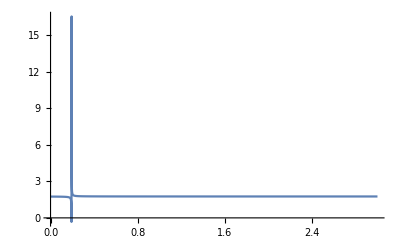

```mathematica
Plot[AacSing/.{L->1,Eab->0.2,Ebc->par,Eac->0.6},{par,0,3},PlotRange->Full]
```

Interesting, it diverges ITSELF .

What does it mean if my divergence  parameter diverges? --> only that my parameters don’t work there. Oh gee.

```mathematica
EabAacSingDivergency = Solve[8 ⅇ^Eab L^2+4 ⅇ^Ebc L^2-ⅇ^(Eab+Ebc) π^2==0,Eab][[1,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Ebc-Log[-(8 L^2-ⅇ^Ebc π^2)/(4 L^2)]

```mathematica
Evaluate[diffFluxB[0] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac->1.6,Eab ->EabAacSingDivergency+1, Ebc ->par2,Eac -> 0.6}]
```

1/(5.46636+3.6 ⅇ^par2-(16.8 ⅇ^(1+Ebc) L^2)/(8 L^2-ⅇ^Ebc π^2))0.00785398 (1.82212+ⅇ^par2-(6.4 ⅇ^(1+Ebc) L^2)/(8 L^2-ⅇ^Ebc π^2)-((64 ⅇ^(1+Ebc+par2) L^2 (-1.56-9.96 signB))/(8 L^2-ⅇ^Ebc π^2)-(16 ⅇ^(1.6+Ebc+par2) L^2 π^2 (-0.6-7.8 signB))/(8 L^2-ⅇ^Ebc π^2)-16 ⅇ^(0.6+par2) (-0.3-6.6 signB)+159.366 signB+57.6 ⅇ^(2 par2) signB-126.331 ⅇ^(0.6+2 (1+Ebc-Log[-(8 L^2-ⅇ^Ebc π^2)/(4 L^2)])) signB-164.23 ⅇ^(par2+2 (1+Ebc-Log[-(8 L^2-ⅇ^Ebc π^2)/(4 L^2)])) signB+155.855 ⅇ^(0.6+par2+2 (1+Ebc-Log[-(8 L^2-ⅇ^Ebc π^2)/(4 L^2)])) signB+107.52 ⅇ^(2 (1+Ebc-Log[-(8 L^2-ⅇ^Ebc π^2)/(4 L^2)])) signB-8 ⅇ^(1.2+par2) π^2 signB-8 ⅇ^(0.6+2 par2) π^2 signB+(410.576 ⅇ^(1+Ebc+2 par2) L^2 signB)/(8 L^2-ⅇ^Ebc π^2)+(32 ⅇ^(2.2+Ebc) L^2 π^2 signB)/(8 L^2-ⅇ^Ebc π^2)-(4 ⅇ^(2.2+Ebc+par2) L^2 π^4 signB)/(8 L^2-ⅇ^Ebc π^2)-(4 ⅇ^(1.6+Ebc+2 par2) L^2 π^4 signB)/(8 L^2-ⅇ^Ebc π^2)-(64 ⅇ^(1.6+Ebc) L^2 (1.9+signB+1.6 (-1+5 signB)))/(8 L^2-ⅇ^Ebc π^2))/(87.4617-(268.8 ⅇ^(1+Ebc) L^2)/(8 L^2-ⅇ^Ebc π^2)+(32 ⅇ^(1.6+Ebc) L^2 π^2)/(8 L^2-ⅇ^Ebc π^2)+ⅇ^par2 (57.6-(4 ⅇ^(1.6+Ebc) L^2 π^4)/(8 L^2-ⅇ^Ebc π^2)-4 π^2 (3.64424-(10.4 ⅇ^(1+Ebc) L^2)/(8 L^2-ⅇ^Ebc π^2)))))

```mathematica
ContourPlot[Evaluate[diffFluxB[0] /.Eab ->EabAacSingDivergency+1/.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac->1.6, Ebc ->par2,Eac -> 0.6}],{par1,0.00001,1},{par2,0.00001,1},PlotRange->All,PlotLegends->Automatic]
```

-Graphics-

I still have a divergency in here, my gosh.

I want to get rid of the divergency right there on top.

```mathematica
Evaluate[diffFluxB1[0,1.385] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Eab ->0.4, Ebc ->0.1,Eac -> 0.6}]
```

diffFluxB1[0,1.385]

```mathematica
Plot[Evaluate[diffFluxB1[0,muOff] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Eab ->0.4, Ebc ->0.1,Eac -> 0.6}],{muOff,0.01,5},PlotRange->Full]
```

-Graphics-

Flux is diverging as I approach the divergency, yes. Need to keep more away from it than 0.5!

```mathematica
Plot[Evaluate[diffFluxB1[0,muOff] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Eab ->0.4, Ebc ->0.1,Eac -> 0.6}],{muOff,0.5,5},PlotRange->Full]
```

-Graphics-

Fuhuck.

```mathematica
Plot[Evaluate[diffFluxB1[0,muOff] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Eab ->0.4, Ebc ->0.1,Eac -> 0.6}],{muOff,2.5,5},PlotRange->Full]
```

-Graphics-

This might actually be physical. I just need to disentangle the divergency (haha) and the physical variation of the flux with the activity.

I mean, this is a parameter space the contour plot actually refuses to plot .

```mathematica
Manipulate[Plot[Evaluate[diffFluxB1[0,muOffset] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Eab ->par1, Ebc ->0.5,Eac -> 0.6}],{par1,0.00001,4}],{muOffset,0.01,3}]
```

### Plot the fluxes

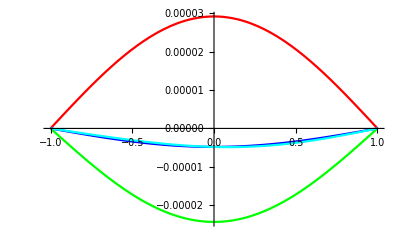

```mathematica
Plot[{Evaluate[diffFluxA[x] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1, per->1}],
Evaluate[diffFluxB[x] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1, per->1}],
Evaluate[diffFluxC[x] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1, per->1}],
Evaluate[diffFluxCalt[x] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1, per->1}]},{x,-1,1},PlotStyle ->{Green, Red,Blue, Cyan}]
```

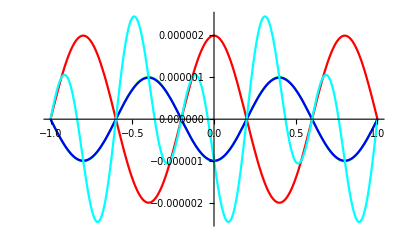

```mathematica
Plot[{Evaluate[diffFluxA[x] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1, per->5}],
Evaluate[diffFluxB[x] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1, per->5}],
Evaluate[diffFluxC[x] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1, per->5}],
Evaluate[diffFluxCalt[x] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1, per->5}]},{x,-1,1},PlotStyle ->{Green, Red,Blue, Cyan}]
```

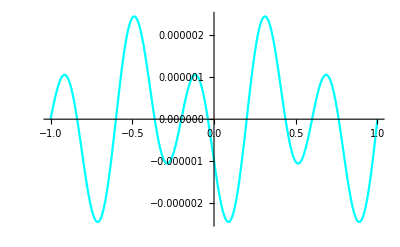

```mathematica
Plot[{Evaluate[diffFluxCalt[x] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.001,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1, per->5}]},{x,-1,1},PlotStyle ->{Green, Red,Blue, Cyan}]
```

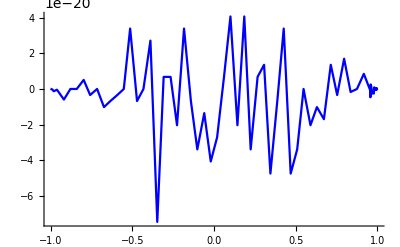

```mathematica
Plot[{Evaluate[diffFluxA[x] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1}]+Evaluate[diffFluxB[x] /.{L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1}]+Evaluate[diffFluxC[x] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6, signA -> 1, signB ->1, signC ->1}]},{x,-1,1},PlotStyle ->{Green, Red,Blue}]
```

```mathematica
Plot[{Evaluate[D[RhoA[x],{x,1}] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6}],
Evaluate[D[RhoB[x],{x,1}] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6}],
Evaluate[D[RhoC[x],{x,1}] /. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6}]},{x,-1,1}, PlotStyle->{Red, Blue, Green}]
```

-Graphics-

```mathematica
D[RhoA[x],{x,1}] /. {L->1, αA ->.5,αB ->1, αC ->1.5, η -> 0.1,μ -> 1.6,ϵAB -> 1.2, ϵBC ->1.3,ϵAC -> 1.3, x ->0}
D[RhoB[x],{x,1}] /. {L->1, αA ->.5,αB ->1, αC ->1.5, η -> 0.1,μ -> 1.6,ϵAB -> 1.2, ϵBC ->1.3,ϵAC -> 1.3, x ->0}
D[RhoC[x],{x,1}] /. {L->1, αA ->.5,αB ->1, αC ->1.5, η -> 0.1,μ -> 1.6,ϵAB -> 1.2, ϵBC ->1.3,ϵAC -> 1.3, x ->0}
```

-((0.0785398 (16 (1+2 Aac) ⅇ^(2 Eab) signA V1a+48 ⅇ^(2 Eac) signA V1a+16 (2+Aac) ⅇ^(2 Ebc) signA V1a-8 ⅇ^(2 Eab+Eac) π^2 signA V1a-8 ⅇ^(Eab+2 Eac) π^2 signA V1a-4 (1+Aac) ⅇ^(2 Eab+Ebc) π^2 signA V1a-8 ⅇ^(2 Eac+Ebc) π^2 signA V1a-4 (1+Aac) ⅇ^(Eab+2 Ebc) π^2 signA V1a-8 ⅇ^(Eac+2 Ebc) π^2 signA V1a+ⅇ^(2 Eab+Eac+Ebc) π^4 signA V1a+ⅇ^(Eab+2 Eac+Ebc) π^4 signA V1a+ⅇ^(Eab+Eac+2 Ebc) π^4 signA V1a+16 ⅇ^(Eac+Ebc) (V1a-Aac V1a+(5+Aac) signA V1a+(-1+Aac) V1b)+32 ⅇ^(Eab+Eac) ((2+Aac) signA V1a+(-1+Aac) (V1b-V1c))-4 ⅇ^(Eab+Eac+Ebc) π^2 ((5+Aac) signA V1a+(-1+Aac) (V1b-V1c))+16 ⅇ^(Eab+Ebc) ((-1+Aac+3 (1+Aac) signA) V1a+V1c-Aac V1c)))/(((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab+48 ⅇ^Eac-8 ⅇ^(Eab+Eac) π^2+ⅇ^Ebc (16 (2+Aac)-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) π^2+ⅇ^(Eab+Eac) π^4))))

-((0.0785398 (16 Aac (1+2 Aac) ⅇ^(2 Eab) signB V1b+48 ⅇ^(2 Eac) signB V1b+16 (2+Aac) ⅇ^(2 Ebc) signB V1b-8 Aac ⅇ^(2 Eab+Eac) π^2 signB V1b-8 ⅇ^(Eab+2 Eac) π^2 signB V1b-4 Aac (1+Aac) ⅇ^(2 Eab+Ebc) π^2 signB V1b-8 ⅇ^(2 Eac+Ebc) π^2 signB V1b-4 (1+Aac) ⅇ^(Eab+2 Ebc) π^2 signB V1b-8 ⅇ^(Eac+2 Ebc) π^2 signB V1b+Aac ⅇ^(2 Eab+Eac+Ebc) π^4 signB V1b+ⅇ^(Eab+2 Eac+Ebc) π^4 signB V1b+ⅇ^(Eab+Eac+2 Ebc) π^4 signB V1b-16 ⅇ^(Eac+Ebc) ((-1+Aac) V1a+V1b-(Aac+(5+Aac) signB) V1b)+16 ⅇ^(Eab+Eac) ((1-Aac+signB+5 Aac signB) V1b+(-1+Aac) V1c)+4 ⅇ^(Eab+Eac+Ebc) π^2 ((-1+Aac) V1a-3 (1+Aac) signB V1b+V1c-Aac V1c)-16 ⅇ^(Eab+Ebc) ((-1+Aac^2) V1a-(1+Aac (4+Aac)) signB V1b+V1c-Aac^2 V1c)))/(((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab+48 ⅇ^Eac-8 ⅇ^(Eab+Eac) π^2+ⅇ^Ebc (16 (2+Aac)-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) π^2+ⅇ^(Eab+Eac) π^4))))

-((0.0785398 (4 Aac^2 (8 ⅇ^(2 Eab) signC V1c-ⅇ^(2 Ebc) (-4+ⅇ^Eab π^2) signC V1c+ⅇ^(Eab+Ebc) (-ⅇ^Eab π^2 signC V1c+4 (V1a-V1c+3 signC V1c)))+4 Aac (4 ⅇ^(2 Eab) signC V1c-ⅇ^(2 Ebc) (-8+ⅇ^Eab π^2) signC V1c+ⅇ^(Eab+Ebc) (-ⅇ^Eab π^2 signC V1c+4 (-V1a+V1c+3 signC V1c)))+Aac ⅇ^Eac (ⅇ^(2 Eab) π^2 (-8+ⅇ^Ebc π^2) signC V1c+8 ⅇ^Ebc (-ⅇ^Ebc π^2 signC V1c+4 (V1a-V1b+2 signC V1c))+ⅇ^Eab (ⅇ^(2 Ebc) π^4 signC V1c-4 ⅇ^Ebc π^2 (V1a-V1b+5 signC V1c)+16 (-V1b+V1c+5 signC V1c)))+ⅇ^Eac (8 ⅇ^Eac (6-ⅇ^Ebc π^2) signC V1c-32 ⅇ^Ebc (V1a-V1b-signC V1c)+ⅇ^Eab (-8 ⅇ^Eac π^2 signC V1c+16 (V1b+(-1+signC) V1c)+ⅇ^Ebc π^2 (ⅇ^Eac π^2 signC V1c-4 (-V1a+V1b+signC V1c))))))/(((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc) (16 (1+2 Aac) ⅇ^Eab+48 ⅇ^Eac-8 ⅇ^(Eab+Eac) π^2+ⅇ^Ebc (16 (2+Aac)-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) π^2+ⅇ^(Eab+Eac) π^4))))

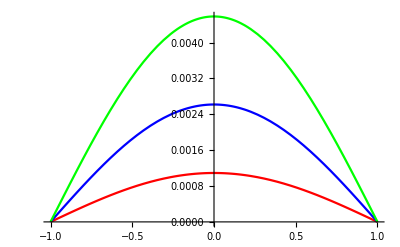

```mathematica
Plot[{Evaluate[ρA0*D[Va[x],{x,1}]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6}],
Evaluate[ρB0*D[Vb[x],{x,1}]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6}],
Evaluate[ρC0*D[Vc[x],{x,1}]/. {L->1, V1a ->.5,V1b ->1, V1c ->1.5, η -> 0.01,Aac -> 1.6,Eab -> 0.6, Ebc ->0.6,Eac -> 0.6}]},{x,-1,1}, PlotStyle->{Red, Blue, Green}]
```

```mathematica
Evaluate[RhoA[x]*D[VA[x],{x,1}]/. {d ->1, L->1, αA ->.5,αB ->1, αC ->1.5, η -> 0.001,μ -> 1.6,ϵAB -> 1.2, ϵBC ->1.3,ϵAC -> 1.3,x->0}]
```

((0.+ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) VA'[0])/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc))

```mathematica
Plot[(D[RhoA[x],x] /. {L->1, αA ->.5,αB ->1, αC ->1.5, η -> 0.1,μ -> 1.6,ϵAB -> 1.2, ϵBC ->1.3,ϵAC -> 1.3})+(RhoA[x]*D[VA[x],{x,1}]/. {d ->1, L->1, αA ->.5,αB ->1, αC ->1.5, η -> 0.1,μ -> 1.6,ϵAB -> 1.2, ϵBC ->1.3,ϵAC -> 1.3}),{x,-1,1},Evaluated->True]
```

-Graphics-

```mathematica
D[VA[x],{x,1}]/. {d ->1, L->1, αA ->.5,αB ->1, αC ->1.5, η -> 0.01,μ -> 1.6,ϵAB -> 1.2, ϵBC ->1.3,ϵAC -> 1.3, x ->0}
D[VB[x],{x,1}]/. {d ->1, L->1, αA ->.5,αB ->1, αC ->1.5, η -> 0.01,μ -> 1.6,ϵAB -> 1.2, ϵBC ->1.3,ϵAC -> 1.3, x ->0}
D[VC[x],{x,1}]/. {d ->1, L->1, αA ->.5,αB ->1, αC ->1.5, η -> 0.01,μ -> 1.6,ϵAB -> 1.2, ϵBC ->1.3,ϵAC -> 1.3, x ->0}
```

VA'[0]

VB'[0]

VC'[0]

Potential times η always of the order 0.1-0.01

```mathematica
Limit[diffFluxA[0]/.{L->1, αA ->0.5,αB ->1., αC ->1.5, η -> 0.1},μ->∞]//FullSimplify
```

1/((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc)0.0785398 ((ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) V1a+(-ⅇ^(2 Ebc) (-4 Aac (-4+ⅇ^Eab π^2)+(-8+ⅇ^Eab π^2) (-4+ⅇ^Eac π^2)) signA V1a+8 (-2 (1+2 Aac) ⅇ^(2 Eab) signA V1a+ⅇ^(2 Eac) (-6+ⅇ^Eab π^2) signA V1a+ⅇ^(Eab+Eac) ((-8-4 Aac+ⅇ^Eab π^2) signA V1a-4 (-1+Aac) (V1b-V1c)))+ⅇ^Ebc (-ⅇ^(2 Eab) π^2 (-4-4 Aac+ⅇ^Eac π^2) signA V1a+8 ⅇ^Eac (ⅇ^Eac π^2 signA V1a-2 (V1a+Aac (-1+signA) V1a+5 signA V1a+(-1+Aac) V1b))+ⅇ^Eab (-ⅇ^(2 Eac) π^4 signA V1a-16 (-1+Aac+3 (1+Aac) signA) V1a+4 ⅇ^Eac π^2 ((5+Aac) signA V1a+(-1+Aac) (V1b-V1c))+16 (-1+Aac) V1c)))/(16 (1+2 Aac) ⅇ^Eab-8 ⅇ^Eac (-6+ⅇ^Eab π^2)+ⅇ^Ebc (-4 Aac (-4+ⅇ^Eab π^2)+(-8+ⅇ^Eab π^2) (-4+ⅇ^Eac π^2))))

```mathematica
diffFluxA[0]/.{L->1, αA ->0.5,αB ->1., αC ->1.5, η -> 0.1}
```

1/((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc)0.0785398 ((ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) V1a-(16 (1+2 Aac) ⅇ^(2 Eab) signA V1a+48 ⅇ^(2 Eac) signA V1a+16 (2+Aac) ⅇ^(2 Ebc) signA V1a-8 ⅇ^(2 Eab+Eac) π^2 signA V1a-8 ⅇ^(Eab+2 Eac) π^2 signA V1a-4 (1+Aac) ⅇ^(2 Eab+Ebc) π^2 signA V1a-8 ⅇ^(2 Eac+Ebc) π^2 signA V1a-4 (1+Aac) ⅇ^(Eab+2 Ebc) π^2 signA V1a-8 ⅇ^(Eac+2 Ebc) π^2 signA V1a+ⅇ^(2 Eab+Eac+Ebc) π^4 signA V1a+ⅇ^(Eab+2 Eac+Ebc) π^4 signA V1a+ⅇ^(Eab+Eac+2 Ebc) π^4 signA V1a+16 ⅇ^(Eac+Ebc) (V1a-Aac V1a+(5+Aac) signA V1a+(-1+Aac) V1b)+32 ⅇ^(Eab+Eac) ((2+Aac) signA V1a+(-1+Aac) (V1b-V1c))-4 ⅇ^(Eab+Eac+Ebc) π^2 ((5+Aac) signA V1a+(-1+Aac) (V1b-V1c))+16 ⅇ^(Eab+Ebc) ((-1+Aac+3 (1+Aac) signA) V1a+V1c-Aac V1c))/(16 (1+2 Aac) ⅇ^Eab+48 ⅇ^Eac-8 ⅇ^(Eab+Eac) π^2+ⅇ^Ebc (16 (2+Aac)-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) π^2+ⅇ^(Eab+Eac) π^4)))

```mathematica
RhoA[x]//FullSimplify
```

1/(2 ((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc))(ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc-((16 (1+2 Aac) ⅇ^(2 Eab) L^4 signA V1a+48 ⅇ^(2 Eac) L^4 signA V1a+16 (2+Aac) ⅇ^(2 Ebc) L^4 signA V1a-8 ⅇ^(2 Eab+Eac) L^2 π^2 signA V1a-8 ⅇ^(Eab+2 Eac) L^2 π^2 signA V1a-4 (1+Aac) ⅇ^(2 Eab+Ebc) L^2 π^2 signA V1a-8 ⅇ^(2 Eac+Ebc) L^2 π^2 signA V1a-4 (1+Aac) ⅇ^(Eab+2 Ebc) L^2 π^2 signA V1a-8 ⅇ^(Eac+2 Ebc) L^2 π^2 signA V1a+ⅇ^(2 Eab+Eac+Ebc) π^4 signA V1a+ⅇ^(Eab+2 Eac+Ebc) π^4 signA V1a+ⅇ^(Eab+Eac+2 Ebc) π^4 signA V1a+16 ⅇ^(Eac+Ebc) L^4 (V1a-Aac V1a+(5+Aac) signA V1a+(-1+Aac) V1b)+32 ⅇ^(Eab+Eac) L^4 ((2+Aac) signA V1a+(-1+Aac) (V1b-V1c))-4 ⅇ^(Eab+Eac+Ebc) L^2 π^2 ((5+Aac) signA V1a+(-1+Aac) (V1b-V1c))+16 ⅇ^(Eab+Ebc) L^4 ((-1+Aac+3 (1+Aac) signA) V1a+V1c-Aac V1c)) η Sin[(π x)/(2 L)])/(16 (1+2 Aac) ⅇ^Eab L^4+48 ⅇ^Eac L^4-8 ⅇ^(Eab+Eac) L^2 π^2+ⅇ^Ebc (16 (2+Aac) L^4-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) L^2 π^2+ⅇ^(Eab+Eac) π^4)))

```mathematica
Plot[{ρA0/.{L->1, ϵAB ->.2,ϵBC ->.2, ϵAC ->.2,αA ->0.5,αB ->1., αC ->1.5, η -> 0.001,μ->mu}},{mu,0,50},PlotRange->All]
```

-Graphics-

```mathematica
Plot[Evaluate[diffFluxA[0]/.{L->1, ϵAB ->.2,ϵBC ->.2, ϵAC ->.2,αA ->0.5,αB ->1., αC ->1.5, η -> 0.001,μ -> mu}],{mu,0,10}, PlotRange->Full]
```

-Graphics-

```mathematica
Plot[Evaluate[diffFluxA[0]/.{L->1, ϵAB ->.2,ϵBC ->.2, ϵAC ->.2,αA ->0.5,αB ->par, αC ->1.5, η -> 0.001,μ -> 1.6}],{par,0,50}, PlotRange->Full]
```

-Graphics-

```mathematica
Plot[Evaluate[diffFluxA[0]/.{L->1, ϵAB ->.2,ϵBC ->.2, ϵAC ->.2,αA ->0.5,αB ->1., αC ->par, η -> 0.001,μ -> 1.6}],{par,0,50}, PlotRange->Full]
```

-Graphics-

```mathematica
Plot[Evaluate[diffFluxA[0]/.{L->1, ϵAB ->par,ϵBC ->.2, ϵAC ->.2,αA ->0.5,αB ->1., αC ->1.5, η -> 0.001,μ -> 1.6}],{par,0,10}, PlotRange->Full]
```

-Graphics-

```mathematica
Plot[Evaluate[diffFluxA[0]/.{L->1, ϵAB ->.2,ϵBC ->par, ϵAC ->.2,αA ->0.5,αB ->1., αC ->1.5, η -> 0.001,μ -> 1.6}],{par,0,10}, PlotRange->Full]
```

-Graphics-

```mathematica
Plot[Evaluate[diffFluxA[0]/.{L->1, ϵAB ->.2,ϵBC ->.2, ϵAC ->par,αA ->0.5,αB ->1., αC ->1.5, η -> 0.001,μ -> 1.6}],{par,0,2}, PlotRange->Full]
```

-Graphics-

```mathematica
vals = Table[RhoA[x]/.{L->1, ϵAB ->.2,ϵBC ->.2, ϵAC ->.2,αA ->0.5,αB ->1., αC ->1.5, η -> 0.01,μ -> 1.6},{x,-1,1,0.0002}];
```

```mathematica
ListPlot[vals]
```

-Graphics-

```mathematica
Plot[RhoA[x]/.{L->1, ϵAB ->.2,ϵBC ->.2, ϵAC ->.2,αA ->0.5,αB ->1., αC ->1.5, η -> 0.01,μ -> 1.6},{x,-1,1}]
```

-Graphics-

```mathematica
diffFluxA[0]/.{L->1, αA ->0.5,αB ->1., αC ->1.5, η -> 0.001,ϵAB ->2.,ϵBC ->2.5}
```

1/((1+2 Aac) ⅇ^Eab+3 ⅇ^Eac+(2+Aac) ⅇ^Ebc)0.000785398 ((ⅇ^Eab+ⅇ^Eac+ⅇ^Ebc) V1a-(16 (1+2 Aac) ⅇ^(2 Eab) signA V1a+48 ⅇ^(2 Eac) signA V1a+16 (2+Aac) ⅇ^(2 Ebc) signA V1a-8 ⅇ^(2 Eab+Eac) π^2 signA V1a-8 ⅇ^(Eab+2 Eac) π^2 signA V1a-4 (1+Aac) ⅇ^(2 Eab+Ebc) π^2 signA V1a-8 ⅇ^(2 Eac+Ebc) π^2 signA V1a-4 (1+Aac) ⅇ^(Eab+2 Ebc) π^2 signA V1a-8 ⅇ^(Eac+2 Ebc) π^2 signA V1a+ⅇ^(2 Eab+Eac+Ebc) π^4 signA V1a+ⅇ^(Eab+2 Eac+Ebc) π^4 signA V1a+ⅇ^(Eab+Eac+2 Ebc) π^4 signA V1a+16 ⅇ^(Eac+Ebc) (V1a-Aac V1a+(5+Aac) signA V1a+(-1+Aac) V1b)+32 ⅇ^(Eab+Eac) ((2+Aac) signA V1a+(-1+Aac) (V1b-V1c))-4 ⅇ^(Eab+Eac+Ebc) π^2 ((5+Aac) signA V1a+(-1+Aac) (V1b-V1c))+16 ⅇ^(Eab+Ebc) ((-1+Aac+3 (1+Aac) signA) V1a+V1c-Aac V1c))/(16 (1+2 Aac) ⅇ^Eab+48 ⅇ^Eac-8 ⅇ^(Eab+Eac) π^2+ⅇ^Ebc (16 (2+Aac)-4 ((1+Aac) ⅇ^Eab+2 ⅇ^Eac) π^2+ⅇ^(Eab+Eac) π^4)))